# (Top Project - dim6 ( Ctw,Cbw,CHud ,C3phiq ) and dim 8 ( C1quWH3 , C1qdWH3 , C2q2H4D , C3 q2H4D ,CudH4D ) - Left Handed Decay width - SM , dim 6 interference )

```mathematica
Quit[]
```

```mathematica
(* Activate FA/FC *)
$LoadFeynArts=True;
$FeynCalcStartupMessages=True;
<<FeynCalc`
$FAVerbose=0;
FAPatch[PatchModelsOnly->True];
```

FeynCalc 10.1.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (24 May 2024) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

Successfully patched FeynArts.

```mathematica
FAPatch[PatchModelsOnly->True,FAModelsDirectory->"/home/user1/Desktop/0000/FEYNCALC/Dim8New/LFullOperator6+8/LAll6and8twb/LFullOperatorAll"];
```

Successfully patched FeynArts.

```mathematica
(* Load FR model *)
InitializeModel["/home/user1/Desktop/0000/FEYNCALC/Dim8New/LFullOperator6+8/LAll6and8twb/LFullOperatorAll/LFullOperatorAll",GenericModel->"/home/user1/Desktop/0000/FEYNCALC/Dim8New/LFullOperator6+8/LAll6and8twb/LFullOperatorAll/LFullOperatorAll"]
```

True

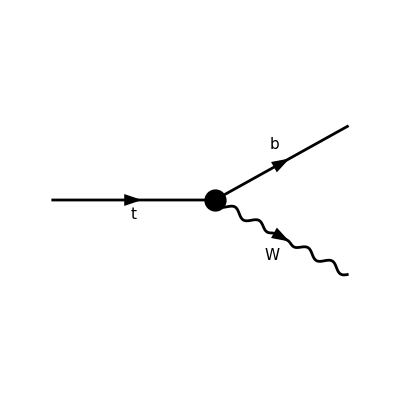

FeynArtsGraphics()(([] | Null | Null | Null | Null | Null))

```mathematica
(* Create diagrams *)
topo=CreateTopologies[0,1->2] (* # of loops = 0 *);

diag=InsertFields[topo,{F[9]}->{F[12], V[3]},InsertionLevel->{Particles},Model->"/home/user1/Desktop/0000/FEYNCALC/Dim8New/LFullOperator6+8/LAll6and8twb/LFullOperatorAll/LFullOperatorAll",GenericModel->"/home/user1/Desktop/0000/FEYNCALC/Dim8New/LFullOperator6+8/LAll6and8twb/LFullOperatorAll/LFullOperatorAll"];
Paint[diag,ColumnsXRows->{6,1},Numbering->None,SheetHeader->False,ImageSize->{800,200}]
```

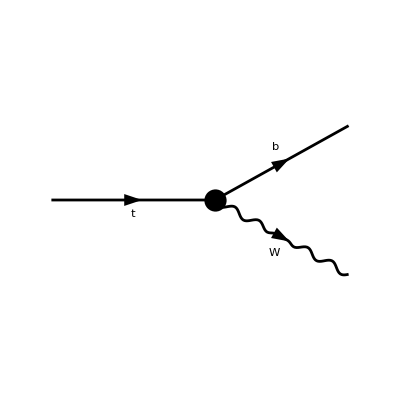

FeynArtsGraphics()(([]))

```mathematica
(* Diagram List *)
NofDiagrams=1;
lsD=Table[diag//DiagramDelete[#,Table[If[j≠i,j],{j,1,NofDiagrams}]/.Null->Sequence[]]&,{i,1,NofDiagrams}];
Paint[lsD[[1]],ColumnsXRows->{1,1},Numbering->None,SheetHeader->False,ImageSize->{200,100}]
```

```mathematica
(* Calculate amplitude *)
lsA0=Table[
FCFAConvert[CreateFeynAmp[lsD[[i]]],IncomingMomenta->{pt},OutgoingMomenta->{pb,pW},ChangeDimension->4,List->False,SMP->False,Contract->True,DropSumOver->True],
{i,1,NofDiagrams}];

lsA0=lsA0[[1]]//FeynAmpDenominatorExplicit//Simplify
(*%//TraditionalForm*)
```

-ⅈ (φ(OverBar[pb],FCGV(MB))).1/(2 Lambda^4)ⅈ δ_Col1Col2 (-vev ((γ̄·OverBar[pW]).(γ̄·(ε̄)^*(pW)).(γ̄)^7-(γ̄·(ε̄)^*(pW)).(γ̄·OverBar[pW]).(γ̄)^7) (vev^2 Conjugate[C1qdWH3]+2 Lambda^2 Conjugate[CbW])-vev Conjugate[CKM3x3] (C1quWH3 vev^2+2 CtW Lambda^2) ((γ̄·OverBar[pW]).(γ̄·(ε̄)^*(pW)).(γ̄)^6-(γ̄·(ε̄)^*(pW)).(γ̄·OverBar[pW]).(γ̄)^6)+2 gc245L Lambda^4 (γ̄·(ε̄)^*(pW)).(γ̄)^7+2 gc245R Lambda^4 (γ̄·(ε̄)^*(pW)).(γ̄)^6).(φ(OverBar[pt],FCGV(MT)))

```mathematica
gc245L = (FCGV["EL"]*(4*Lambda^4 + 2*C2q2H4D*vev^4 + C3q2H4D*vev^4 + 2*vev^4*Conjugate[C2q2H4D] + 4*Lambda^2*vev^2*Conjugate[C3phiq] - vev^4*Conjugate[C3q2H4D])*Conjugate[CKM3x3])/(4*Sqrt[2]*Lambda^4*sw);gc245R = (FCGV["EL"]*(Lambda^2*vev^2*Conjugate[CHud] + vev^4*Conjugate[CudH4D]))/(2*Sqrt[2]*Lambda^4*sw);
sw=e/g;
```

```mathematica
lsA0//FullSimplify
```

-ⅈ (φ(OverBar[pb],FCGV(MB))).1/(8 e Lambda^4)ⅈ δ_Col1Col2 (-4 e vev ((γ̄·OverBar[pW]).(γ̄·(ε̄)^*(pW)).(γ̄)^7-(γ̄·(ε̄)^*(pW)).(γ̄·OverBar[pW]).(γ̄)^7) (vev^2 Conjugate[C1qdWH3]+2 Lambda^2 Conjugate[CbW])-4 e vev Conjugate[CKM3x3] (C1quWH3 vev^2+2 CtW Lambda^2) ((γ̄·OverBar[pW]).(γ̄·(ε̄)^*(pW)).(γ̄)^6-(γ̄·(ε̄)^*(pW)).(γ̄·OverBar[pW]).(γ̄)^6)+2 √2 g Conjugate[CKM3x3] FCGV(EL) (γ̄·(ε̄)^*(pW)).(γ̄)^7 (vev^4 (Conjugate[C2q2H4D]+C2q2H4D-Re(C3q2H4D)+C3q2H4D)+2 Lambda^2 vev^2 Conjugate[C3phiq]+2 Lambda^4)+2 √2 g vev^2 FCGV(EL) (γ̄·(ε̄)^*(pW)).(γ̄)^6 (Lambda^2 Conjugate[CHud]+vev^2 Conjugate[CudH4D])).(φ(OverBar[pt],FCGV(MT)))

```mathematica
(* Simplify *)
(* Setup the kinematics *)
SetMandelstam[s,t,u,pt,pb,pW,mpt,mpb,mpW];

rep0={EL->e,CW->cW,SW->sW,MW->mW,ME->0,MB->mb,MT->mt,
Pair[Momentum[pt],Momentum[pt]]->mt^2,
Pair[Momentum[pb],Momentum[pb]]->mb^2,
Pair[Momentum[pW],Momentum[pW]]->mW^2};
lsA=(lsA0//ReplaceAll@{FCGV[x_String]:>ToExpression[x]}(*//DiracSimplify*))/.rep0
```

-ⅈ (φ(OverBar[pb],mb)).1/(2 Lambda^4)ⅈ δ_Col1Col2 (-vev ((γ̄·OverBar[pW]).(γ̄·(ε̄)^*(pW)).(γ̄)^7-(γ̄·(ε̄)^*(pW)).(γ̄·OverBar[pW]).(γ̄)^7) (vev^2 Conjugate[C1qdWH3]+2 Lambda^2 Conjugate[CbW])-vev Conjugate[CKM3x3] (C1quWH3 vev^2+2 CtW Lambda^2) ((γ̄·OverBar[pW]).(γ̄·(ε̄)^*(pW)).(γ̄)^6-(γ̄·(ε̄)^*(pW)).(γ̄·OverBar[pW]).(γ̄)^6)+(g Conjugate[CKM3x3] (γ̄·(ε̄)^*(pW)).(γ̄)^7 (2 vev^4 Conjugate[C2q2H4D]+2 C2q2H4D vev^4+4 Lambda^2 vev^2 Conjugate[C3phiq]-vev^4 Conjugate[C3q2H4D]+C3q2H4D vev^4+4 Lambda^4))/(2 √2)+(g (γ̄·(ε̄)^*(pW)).(γ̄)^6 (Lambda^2 vev^2 Conjugate[CHud]+vev^4 Conjugate[CudH4D]))/(√2)).(φ(OverBar[pt],mt))

```mathematica
Fspin[x_]:=x//SUNFDeltaContract//FermionSpinSum[#,ExtraFactor->1/2]&//ReplaceAll[#,DiracTrace->TR]&
(lsAsq=(lsA*ComplexConjugate[lsA])//Simplify//Fspin//Contract)
```

```mathematica
lsAsqq=lsAsq/.{SUNN->Nc}//FullSimplify
```

1/(32 Lambda^8)Nc (4 g^2 Lambda^4 (Conjugate[CHud])^2 (ⅈ (ϵ̄)^(OverBar[pb]OverBar[pt](ε̄)^*(pW)ε̄(pW))+(OverBar[pb]·ε̄(pW)) (OverBar[pt]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pt]·ε̄(pW))-(OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))) vev^4+8 g Lambda^2 Conjugate[CHud] (g Conjugate[CudH4D] (ⅈ (ϵ̄)^(OverBar[pb]OverBar[pt](ε̄)^*(pW)ε̄(pW))+(OverBar[pb]·ε̄(pW)) (OverBar[pt]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pt]·ε̄(pW))-(OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))) vev^4+√2 mt (2 Conjugate[CbW] Lambda^2+vev^2 Conjugate[C1qdWH3]) (2 ⅈ (ϵ̄)^(OverBar[pb]OverBar[pW](ε̄)^*(pW)ε̄(pW))+(OverBar[pb]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-2 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))) vev+mb Conjugate[CKM3x3] (ⅈ √2 vev (2 CtW Lambda^2+C1quWH3 vev^2) (2 (ϵ̄)^(OverBar[pt]OverBar[pW](ε̄)^*(pW)ε̄(pW))+ⅈ ((OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+(OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))))+((ε̄)^*(pW)·ε̄(pW)) (2 g Lambda^2 mt Conjugate[C3phiq] vev^2+2 √2 (2 CtW Lambda^2+C1quWH3 vev^2) (OverBar[pt]·OverBar[pW]) vev+g mt (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))))) vev^2+4 mb Conjugate[CKM3x3] (2 g Conjugate[CudH4D] (ⅈ √2 vev (2 CtW Lambda^2+C1quWH3 vev^2) (2 (ϵ̄)^(OverBar[pt]OverBar[pW](ε̄)^*(pW)ε̄(pW))+ⅈ ((OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+(OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))))+((ε̄)^*(pW)·ε̄(pW)) (2 g Lambda^2 mt Conjugate[C3phiq] vev^2+2 √2 (2 CtW Lambda^2+C1quWH3 vev^2) (OverBar[pt]·OverBar[pW]) vev+g mt (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D))))) vev^3+Conjugate[C1qdWH3] (-16 mt vev (2 CtW Lambda^2+C1quWH3 vev^2) ((OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-OverBar[pW]^2 ((ε̄)^*(pW)·ε̄(pW)))-4 ⅈ √2 g (ϵ̄)^(OverBar[pt]OverBar[pW](ε̄)^*(pW)ε̄(pW)) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))-2 √2 g ((OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-2 (OverBar[pt]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))-2 √2 g (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))) vev^2+4 Lambda^2 Conjugate[CbW] (-8 mt vev (2 CtW Lambda^2+C1quWH3 vev^2) ((OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-OverBar[pW]^2 ((ε̄)^*(pW)·ε̄(pW)))-2 ⅈ √2 g (ϵ̄)^(OverBar[pt]OverBar[pW](ε̄)^*(pW)ε̄(pW)) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))-√2 g (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))-√2 g ((OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-2 (OverBar[pt]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D))))) vev+4 (g^2 (Conjugate[CudH4D])^2 (ⅈ (ϵ̄)^(OverBar[pb]OverBar[pt](ε̄)^*(pW)ε̄(pW))+(OverBar[pb]·ε̄(pW)) (OverBar[pt]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pt]·ε̄(pW))-(OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))) vev^8+2 √2 g mt (2 Conjugate[CbW] Lambda^2+vev^2 Conjugate[C1qdWH3]) Conjugate[CudH4D] (2 ⅈ (ϵ̄)^(OverBar[pb]OverBar[pW](ε̄)^*(pW)ε̄(pW))+(OverBar[pb]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-2 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))) vev^5+8 (Conjugate[C1qdWH3] vev^3+2 Lambda^2 Conjugate[CbW] vev)^2 (2 ⅈ (ϵ̄)^(OverBar[pb]OverBar[pW](ε̄)^*(pW)ε̄(pW)) (OverBar[pt]·OverBar[pW])+(OverBar[pb]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) (OverBar[pt]·OverBar[pW])+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) (OverBar[pt]·OverBar[pW])+(OverBar[pb]·OverBar[pW]) (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+(OverBar[pb]·OverBar[pW]) (OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-(OverBar[pb]·OverBar[pt]) (OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-ⅈ (((ϵ̄)^(OverBar[pb]OverBar[pt](ε̄)^*(pW)ε̄(pW))-ⅈ ((OverBar[pb]·ε̄(pW)) (OverBar[pt]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pt]·ε̄(pW)))) OverBar[pW]^2-(ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW]ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+(ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW](ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)))+((OverBar[pb]·OverBar[pt]) OverBar[pW]^2-2 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·OverBar[pW])) ((ε̄)^*(pW)·ε̄(pW))))+(Conjugate[CKM3x3])^2 (-16 g^2 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^8-32 g^2 vev^2 Conjugate[C3phiq] (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^6-64 √2 CtW g mt vev (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^6-128 ⅈ CtW^2 vev^2 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW]ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) Lambda^4+128 CtW^2 vev^2 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) Lambda^4+128 ⅈ CtW^2 vev^2 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW](ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^4+128 CtW^2 vev^2 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^4-128 CtW^2 vev^2 (OverBar[pb]·OverBar[pt]) (OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^4-16 g^2 vev^4 (Conjugate[C3phiq])^2 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^4-16 ⅈ g^2 vev^4 Im(C3q2H4D) (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^4-32 √2 C1quWH3 g mt vev^3 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^4-64 √2 CtW g mt vev^3 Conjugate[C3phiq] (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^4-256 CtW^2 vev^2 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^4+128 CtW^2 vev^2 (OverBar[pb]·OverBar[pt]) OverBar[pW]^2 ((ε̄)^*(pW)·ε̄(pW)) Lambda^4-32 g^2 vev^4 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D) Lambda^4-128 ⅈ C1quWH3 CtW vev^4 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW]ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) Lambda^2+128 C1quWH3 CtW vev^4 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) Lambda^2+128 ⅈ C1quWH3 CtW vev^4 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW](ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^2+128 C1quWH3 CtW vev^4 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^2-128 C1quWH3 CtW vev^4 (OverBar[pb]·OverBar[pt]) (OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^2-8 C3q2H4D g^2 vev^6 Conjugate[C3phiq] (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^2+8 g^2 vev^6 Conjugate[C3phiq] Conjugate[C3q2H4D] (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^2-32 √2 C3q2H4D CtW g mt vev^5 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^2-32 √2 C1quWH3 g mt vev^5 Conjugate[C3phiq] (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^2-256 C1quWH3 CtW vev^4 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^2+128 C1quWH3 CtW vev^4 (OverBar[pb]·OverBar[pt]) OverBar[pW]^2 ((ε̄)^*(pW)·ε̄(pW)) Lambda^2-32 g^2 vev^6 Conjugate[C3phiq] (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D) Lambda^2-64 √2 CtW g mt vev^5 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D) Lambda^2+32 √2 CtW g mt vev^5 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Re(C3q2H4D) Lambda^2-32 ⅈ C1quWH3^2 vev^6 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW]ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+32 C1quWH3^2 vev^6 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+32 ⅈ C1quWH3^2 vev^6 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW](ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))+32 C1quWH3^2 vev^6 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-32 C1quWH3^2 vev^6 (OverBar[pb]·OverBar[pt]) (OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))+4 C2q2H4D^2 g^2 vev^8 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))-3 C3q2H4D^2 g^2 vev^8 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))-4 g^2 vev^8 (Conjugate[C2q2H4D])^2 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))-g^2 vev^8 (Conjugate[C3q2H4D])^2 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))-16 ⅈ √2 C1quWH3 g mt vev^7 Im(C3q2H4D) (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))-64 C1quWH3^2 vev^6 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))+32 C1quWH3^2 vev^6 (OverBar[pb]·OverBar[pt]) OverBar[pW]^2 ((ε̄)^*(pW)·ε̄(pW))-16 C2q2H4D g^2 vev^8 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D)-16 ⅈ g^2 vev^8 Im(C3q2H4D) (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D)-32 √2 C1quWH3 g mt vev^7 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D)-ⅈ (ϵ̄)^(OverBar[pb]OverBar[pt](ε̄)^*(pW)ε̄(pW)) (4 g^2 (Conjugate[C2q2H4D])^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 (Conjugate[C3q2H4D])^2 vev^6-2 C3q2H4D g^2 Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 (Conjugate[C3phiq])^2 vev^2+32 g^2 Lambda^4 Re(C2q2H4D) vev^2+16 ⅈ g^2 Im(C3q2H4D) (Lambda^4+vev^4 Re(C2q2H4D)) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+ⅈ vev^4 Im(C3q2H4D))-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 OverBar[pW]^2) vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))-16 ⅈ vev (2 CtW Lambda^2+C1quWH3 vev^2) (ϵ̄)^(OverBar[pb]OverBar[pW](ε̄)^*(pW)ε̄(pW)) (4 vev (2 CtW Lambda^2+C1quWH3 vev^2) (OverBar[pt]·OverBar[pW])+√2 g mt (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D))))+4 C3q2H4D g^2 vev^8 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Re(C3q2H4D)+(OverBar[pb]·ε̄(pW)) ((OverBar[pt]·(ε̄)^*(pW)) (4 g^2 (Conjugate[C2q2H4D])^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 (Conjugate[C3q2H4D])^2 vev^6-2 C3q2H4D g^2 Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 (Conjugate[C3phiq])^2 vev^2+32 g^2 Lambda^4 Re(C2q2H4D) vev^2+16 ⅈ g^2 Im(C3q2H4D) (Lambda^4+vev^4 Re(C2q2H4D)) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+ⅈ vev^4 Im(C3q2H4D))-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 OverBar[pW]^2) vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))+8 vev (OverBar[pW]·(ε̄)^*(pW)) (4 vev (OverBar[pt]·OverBar[pW]) (2 CtW Lambda^2+C1quWH3 vev^2)^2+√2 g mt (4 CtW Lambda^6+2 C1quWH3 vev^2 Lambda^4+2 vev^2 (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[C3phiq] Lambda^2+C1quWH3 C3q2H4D vev^6+vev^4 (2 ⅈ CtW Im(C3q2H4D) Lambda^2+2 (2 CtW Lambda^2+C1quWH3 vev^2) Re(C2q2H4D)-C1quWH3 vev^2 Re(C3q2H4D)))))+(OverBar[pb]·(ε̄)^*(pW)) ((OverBar[pt]·ε̄(pW)) (4 g^2 (Conjugate[C2q2H4D])^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 (Conjugate[C3q2H4D])^2 vev^6-2 C3q2H4D g^2 Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 (Conjugate[C3phiq])^2 vev^2+32 g^2 Lambda^4 Re(C2q2H4D) vev^2+16 ⅈ g^2 Im(C3q2H4D) (Lambda^4+vev^4 Re(C2q2H4D)) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+ⅈ vev^4 Im(C3q2H4D))-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 OverBar[pW]^2) vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))+8 vev (OverBar[pW]·ε̄(pW)) (4 vev (OverBar[pt]·OverBar[pW]) (2 CtW Lambda^2+C1quWH3 vev^2)^2+√2 g mt (4 CtW Lambda^6+2 C1quWH3 vev^2 Lambda^4+2 vev^2 (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[C3phiq] Lambda^2+C1quWH3 C3q2H4D vev^6+vev^4 (2 ⅈ CtW Im(C3q2H4D) Lambda^2+2 (2 CtW Lambda^2+C1quWH3 vev^2) Re(C2q2H4D)-C1quWH3 vev^2 Re(C3q2H4D)))))))

1/(32 Lambda^8)Nc (4 g^2 Lambda^4 (Conjugate[CHud])^2 (ⅈ (ϵ̄)^(OverBar[pb]OverBar[pt](ε̄)^*(pW)ε̄(pW))+(OverBar[pb]·ε̄(pW)) (OverBar[pt]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pt]·ε̄(pW))-(OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))) vev^4+8 g Lambda^2 Conjugate[CHud] (g Conjugate[CudH4D] (ⅈ (ϵ̄)^(OverBar[pb]OverBar[pt](ε̄)^*(pW)ε̄(pW))+(OverBar[pb]·ε̄(pW)) (OverBar[pt]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pt]·ε̄(pW))-(OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))) vev^4+√2 mt (2 Conjugate[CbW] Lambda^2+vev^2 Conjugate[C1qdWH3]) (2 ⅈ (ϵ̄)^(OverBar[pb]OverBar[pW](ε̄)^*(pW)ε̄(pW))+(OverBar[pb]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-2 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))) vev+mb Conjugate[CKM3x3] (ⅈ √2 vev (2 CtW Lambda^2+C1quWH3 vev^2) (2 (ϵ̄)^(OverBar[pt]OverBar[pW](ε̄)^*(pW)ε̄(pW))+ⅈ ((OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+(OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))))+((ε̄)^*(pW)·ε̄(pW)) (2 g Lambda^2 mt Conjugate[C3phiq] vev^2+2 √2 (2 CtW Lambda^2+C1quWH3 vev^2) (OverBar[pt]·OverBar[pW]) vev+g mt (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))))) vev^2+

```mathematica
(1/(32 Lambda^8))*Nc*(4 g^2 Lambda^4 Conjugate[CHud]^2*(I LeviCivitaContraction[pb,pt,Epclh,Eplh]+MinkSP[pb,Eplh]*MinkSP[pt,Epclh]+MinkSP[pb,Epclh]*MinkSP[pt,Eplh]-MinkSP[pb,pt]*MinkSP[Epclh,Eplh])*vev^4+8 g Lambda^2 Conjugate[CHud]*(g Conjugate[CudH4D]*(I LeviCivitaContraction[pb,pt,Epclh,Eplh]+MinkSP[pb,Eplh]*MinkSP[pt,Epclh]+MinkSP[pb,Epclh]*MinkSP[pt,Eplh]-MinkSP[pb,pt]*MinkSP[Epclh,Eplh])*vev^4+Sqrt[2]*mt*(2 Conjugate[CbW]*Lambda^2+vev^2*Conjugate[C1qdWH3])*(2 I LeviCivitaContraction[pb,pW,Epclh,Eplh]+MinkSP[pb,Eplh]*MinkSP[pW,Epclh]+MinkSP[pb,Epclh]*MinkSP[pW,Eplh]-2 MinkSP[pb,pW]*MinkSP[Epclh,Eplh])*vev+mb*Conjugate[CKM3x3]*(I Sqrt[2]*vev*(2 CtW*Lambda^2+C1quWH3*vev^2)*(2 LeviCivitaContraction[pt,pW,Epclh,Eplh]+I (MinkSP[pt,Eplh]*MinkSP[pW,Epclh]+MinkSP[pt,Epclh]*MinkSP[pW,Eplh]))+MinkSP[Epclh,Eplh]*(2 g Lambda^2*mt*Conjugate[C3phiq]*vev^2+2 Sqrt[2]*(2 CtW*Lambda^2+C1quWH3*vev^2)*MinkSP[pt,pW]*vev+g*mt*(2 Lambda^4+C3q2H4D*vev^4+vev^4*(C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))))*vev^2+
```

4 mb Conjugate[CKM3x3] (2 g Conjugate[CudH4D] (ⅈ √2 vev (2 CtW Lambda^2+C1quWH3 vev^2) (2 (ϵ̄)^(OverBar[pt]OverBar[pW](ε̄)^*(pW)ε̄(pW))+ⅈ ((OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+(OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))))+((ε̄)^*(pW)·ε̄(pW)) (2 g Lambda^2 mt Conjugate[C3phiq] vev^2+2 √2 (2 CtW Lambda^2+C1quWH3 vev^2) (OverBar[pt]·OverBar[pW]) vev+g mt (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D))))) vev^3+Conjugate[C1qdWH3] (-16 mt vev (2 CtW Lambda^2+C1quWH3 vev^2) ((OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-OverBar[pW]^2 ((ε̄)^*(pW)·ε̄(pW)))-4 ⅈ √2 g (ϵ̄)^(OverBar[pt]OverBar[pW](ε̄)^*(pW)ε̄(pW)) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))-2 √2 g ((OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-2 (OverBar[pt]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))-

```mathematica
4 mb Conjugate[CKM3x3]*(2 g Conjugate[CudH4D]*(I Sqrt[2] vev (2 CtW Lambda^2+C1quWH3 vev^2)*(2 LeviCivitaContraction[pt,pW,Epclh,Eplh]+I (MinkSP[pt,Eplh]*MinkSP[pW,Epclh]+MinkSP[pt,Epclh]*MinkSP[pW,Eplh]))+MinkSP[Epclh,Eplh]*(2 g Lambda^2 mt Conjugate[C3phiq] vev^2+2 Sqrt[2] (2 CtW Lambda^2+C1quWH3 vev^2) MinkSP[pt,pW] vev+g mt (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))*vev^3+Conjugate[C1qdWH3]*(-16 mt vev (2 CtW Lambda^2+C1quWH3 vev^2)*(MinkSP[pW,Epclh]*MinkSP[pW,Eplh]-MinkSP[pW,pW]*MinkSP[Epclh,Eplh])-4 I Sqrt[2] g LeviCivitaContraction[pt,pW,Epclh,Eplh]*(2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-2 Sqrt[2] g*(MinkSP[pt,Epclh]*MinkSP[pW,Eplh]-2 MinkSP[pt,pW]*MinkSP[Epclh,Eplh])*(2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-
```

2 √2 g (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))) vev^2+4 Lambda^2 Conjugate[CbW] (-8 mt vev (2 CtW Lambda^2+C1quWH3 vev^2) ((OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-OverBar[pW]^2 ((ε̄)^*(pW)·ε̄(pW)))-2 ⅈ √2 g (ϵ̄)^(OverBar[pt]OverBar[pW](ε̄)^*(pW)ε̄(pW)) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))-√2 g (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))-√2 g ((OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-2 (OverBar[pt]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D))))) vev+

```mathematica
2 Sqrt[2] g MinkSP[pt,Eplh] MinkSP[pW,Epclh]*(2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))*vev^2
+4 Lambda^2 Conjugate[CbW]*(-8 mt vev (2 CtW Lambda^2+C1quWH3 vev^2)*(MinkSP[pW,Epclh]*MinkSP[pW,Eplh]-MinkSP[pW,pW]*MinkSP[Epclh,Eplh])-2 I Sqrt[2] g LeviCivitaContraction[pt,pW,Epclh,Eplh]*(2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-Sqrt[2] g MinkSP[pt,Eplh]*MinkSP[pW,Epclh]*(2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-Sqrt[2] g*(MinkSP[pt,Epclh]*MinkSP[pW,Eplh]-2 MinkSP[pt,pW]*MinkSP[Epclh,Eplh])*(2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))*vev+
```

4 (g^2 (Conjugate[CudH4D])^2 (ⅈ (ϵ̄)^(OverBar[pb]OverBar[pt](ε̄)^*(pW)ε̄(pW))+(OverBar[pb]·ε̄(pW)) (OverBar[pt]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pt]·ε̄(pW))-(OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))) vev^8+2 √2 g mt (2 Conjugate[CbW] Lambda^2+vev^2 Conjugate[C1qdWH3]) Conjugate[CudH4D] (2 ⅈ (ϵ̄)^(OverBar[pb]OverBar[pW](ε̄)^*(pW)ε̄(pW))+(OverBar[pb]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-2 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))) vev^5+8 (Conjugate[C1qdWH3] vev^3+2 Lambda^2 Conjugate[CbW] vev)^2 (2 ⅈ (ϵ̄)^(OverBar[pb]OverBar[pW](ε̄)^*(pW)ε̄(pW)) (OverBar[pt]·OverBar[pW])+(OverBar[pb]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) (OverBar[pt]·OverBar[pW])+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) (OverBar[pt]·OverBar[pW])+(OverBar[pb]·OverBar[pW]) (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+(OverBar[pb]·OverBar[pW]) (OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-(OverBar[pb]·OverBar[pt]) (OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-ⅈ (((ϵ̄)^(OverBar[pb]OverBar[pt](ε̄)^*(pW)ε̄(pW))-ⅈ ((OverBar[pb]·ε̄(pW)) (OverBar[pt]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pt]·ε̄(pW)))) OverBar[pW]^2-(ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW]ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+(ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW](ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)))+((OverBar[pb]·OverBar[pt]) OverBar[pW]^2-2 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·OverBar[pW])) ((ε̄)^*(pW)·ε̄(pW))))+

```mathematica
4 (g^2 Conjugate[CudH4D]^2*(I LeviCivitaContraction[pb,pt,Epclh,Eplh]+MinkSP[pb,Eplh]*MinkSP[pt,Epclh]+MinkSP[pb,Epclh]*MinkSP[pt,Eplh]-MinkSP[pb,pt]*MinkSP[Epclh,Eplh])*vev^8+2 Sqrt[2] g mt (2 Conjugate[CbW] Lambda^2+vev^2 Conjugate[C1qdWH3])*Conjugate[CudH4D]*(2 I LeviCivitaContraction[pb,pW,Epclh,Eplh]+MinkSP[pb,Eplh]*MinkSP[pW,Epclh]+MinkSP[pb,Epclh]*MinkSP[pW,Eplh]-2 MinkSP[pb,pW]*MinkSP[Epclh,Eplh])*vev^5+8 (Conjugate[C1qdWH3] vev^3+2 Lambda^2 Conjugate[CbW] vev)^2*(2 I LeviCivitaContraction[pb,pW,Epclh,Eplh]*MinkSP[pt,pW]+MinkSP[pb,Eplh]*MinkSP[pW,Epclh]*MinkSP[pt,pW]+MinkSP[pb,Epclh]*MinkSP[pW,Eplh]*MinkSP[pt,pW]+MinkSP[pb,pW]*MinkSP[pt,Eplh]*MinkSP[pW,Epclh]+MinkSP[pb,pW]*MinkSP[pt,Epclh]*MinkSP[pW,Eplh]-MinkSP[pb,pt]*MinkSP[pW,Epclh]*MinkSP[pW,Eplh]-I ((LeviCivitaContraction[pb,pt,Epclh,Eplh]-I (MinkSP[pb,Eplh]*MinkSP[pt,Epclh]+MinkSP[pb,Epclh]*MinkSP[pt,Eplh]))*MinkSP[pW,pW]-LeviCivitaContraction[pb,pt,pW,Eplh]*MinkSP[pW,Epclh]+LeviCivitaContraction[pb,pt,pW,Epclh]*MinkSP[pW,Eplh])+(MinkSP[pb,pt]*MinkSP[pW,pW]-2 MinkSP[pb,pW]*MinkSP[pt,pW])*MinkSP[Epclh,Eplh]))+
```

(Conjugate[CKM3x3])^2 (-16 g^2 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^8-32 g^2 vev^2 Conjugate[C3phiq] (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^6-64 √2 CtW g mt vev (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^6-128 ⅈ CtW^2 vev^2 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW]ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) Lambda^4+128 CtW^2 vev^2 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) Lambda^4+128 ⅈ CtW^2 vev^2 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW](ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^4+128 CtW^2 vev^2 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^4-128 CtW^2 vev^2 (OverBar[pb]·OverBar[pt]) (OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^4-16 g^2 vev^4 (Conjugate[C3phiq])^2 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^4-16 ⅈ g^2 vev^4 Im(C3q2H4D) (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^4-32 √2 C1quWH3 g mt vev^3 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^4-64 √2 CtW g mt vev^3 Conjugate[C3phiq] (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^4-256 CtW^2 vev^2 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^4+

```mathematica
Conjugate[CKM3x3]^2*(-16 g^2 MinkSP[pb,pt] MinkSP[Epclh,Eplh] Lambda^8-32 g^2 vev^2 Conjugate[C3phiq] MinkSP[pb,pt] MinkSP[Epclh,Eplh] Lambda^6-64 Sqrt[2] CtW g mt vev MinkSP[pb,pW] MinkSP[Epclh,Eplh] Lambda^6-128 I CtW^2 vev^2 LeviCivitaContraction[pb,pt,pW,Eplh] MinkSP[pW,Epclh] Lambda^4+128 CtW^2 vev^2 MinkSP[pb,pW] MinkSP[pt,Eplh] MinkSP[pW,Epclh] Lambda^4+128 I CtW^2 vev^2 LeviCivitaContraction[pb,pt,pW,Epclh] MinkSP[pW,Eplh] Lambda^4+128 CtW^2 vev^2 MinkSP[pb,pW] MinkSP[pt,Epclh] MinkSP[pW,Eplh] Lambda^4-128 CtW^2 vev^2 MinkSP[pb,pt] MinkSP[pW,Epclh] MinkSP[pW,Eplh] Lambda^4-16 g^2 vev^4 (Conjugate[C3phiq])^2 MinkSP[pb,pt] MinkSP[Epclh,Eplh] Lambda^4-16 I g^2 vev^4 Im[C3q2H4D] MinkSP[pb,pt] MinkSP[Epclh,Eplh] Lambda^4-32 Sqrt[2] C1quWH3 g mt vev^3 MinkSP[pb,pW] MinkSP[Epclh,Eplh] Lambda^4-64 Sqrt[2] CtW g mt vev^3 Conjugate[C3phiq] MinkSP[pb,pW] MinkSP[Epclh,Eplh] Lambda^4-256 CtW^2 vev^2 MinkSP[pb,pW] MinkSP[pt,pW] MinkSP[Epclh,Eplh] Lambda^4+
```

128 CtW^2 vev^2 (OverBar[pb]·OverBar[pt]) OverBar[pW]^2 ((ε̄)^*(pW)·ε̄(pW)) Lambda^4-32 g^2 vev^4 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D) Lambda^4-128 ⅈ C1quWH3 CtW vev^4 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW]ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) Lambda^2+128 C1quWH3 CtW vev^4 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) Lambda^2+128 ⅈ C1quWH3 CtW vev^4 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW](ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^2+128 C1quWH3 CtW vev^4 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^2-128 C1quWH3 CtW vev^4 (OverBar[pb]·OverBar[pt]) (OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^2-8 C3q2H4D g^2 vev^6 Conjugate[C3phiq] (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^2+8 g^2 vev^6 Conjugate[C3phiq] Conjugate[C3q2H4D] (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^2-32 √2 C3q2H4D CtW g mt vev^5 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^2-32 √2 C1quWH3 g mt vev^5 Conjugate[C3phiq] (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^2-256 C1quWH3 CtW vev^4 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^2+128 C1quWH3 CtW vev^4 (OverBar[pb]·OverBar[pt]) OverBar[pW]^2 ((ε̄)^*(pW)·ε̄(pW)) Lambda^2-32 g^2 vev^6 Conjugate[C3phiq] (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D) Lambda^2-64 √2 CtW g mt vev^5 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D) Lambda^2+

```mathematica
128 CtW^2 vev^2 MinkSP[pb,pt] MinkSP[pW,pW] MinkSP[Epclh,Eplh] Lambda^4-32 g^2 vev^4 MinkSP[pb,pt] MinkSP[Epclh,Eplh] Re[C2q2H4D] Lambda^4-128 I C1quWH3 CtW vev^4 LeviCivitaContraction[pb,pt,pW,Eplh] MinkSP[pW,Epclh] Lambda^2+128 C1quWH3 CtW vev^4 MinkSP[pb,pW] MinkSP[pt,Eplh] MinkSP[pW,Epclh] Lambda^2+128 I C1quWH3 CtW vev^4 LeviCivitaContraction[pb,pt,pW,Epclh] MinkSP[pW,Eplh] Lambda^2+128 C1quWH3 CtW vev^4 MinkSP[pb,pW] MinkSP[pt,Epclh] MinkSP[pW,Eplh] Lambda^2-128 C1quWH3 CtW vev^4 MinkSP[pb,pt] MinkSP[pW,Epclh] MinkSP[pW,Eplh] Lambda^2-8 C3q2H4D g^2 vev^6 Conjugate[C3phiq] MinkSP[pb,pt] MinkSP[Epclh,Eplh] Lambda^2+8 g^2 vev^6 Conjugate[C3phiq] Conjugate[C3q2H4D] MinkSP[pb,pt] MinkSP[Epclh,Eplh] Lambda^2-32 Sqrt[2] C3q2H4D CtW g mt vev^5 MinkSP[pb,pW] MinkSP[Epclh,Eplh] Lambda^2-32 Sqrt[2] C1quWH3 g mt vev^5 Conjugate[C3phiq] MinkSP[pb,pW] MinkSP[Epclh,Eplh] Lambda^2-256 C1quWH3 CtW vev^4 MinkSP[pb,pW] MinkSP[pt,pW] MinkSP[Epclh,Eplh] Lambda^2+128 C1quWH3 CtW vev^4 MinkSP[pb,pt] MinkSP[pW,pW] MinkSP[Epclh,Eplh] Lambda^2-32 g^2 vev^6 Conjugate[C3phiq] MinkSP[pb,pt] MinkSP[Epclh,Eplh] Re[C2q2H4D] Lambda^2-64 Sqrt[2] CtW g mt vev^5 MinkSP[pb,pW] MinkSP[Epclh,Eplh] Re[C2q2H4D] Lambda^2+
```

32 √2 CtW g mt vev^5 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Re(C3q2H4D) Lambda^2-32 ⅈ C1quWH3^2 vev^6 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW]ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+32 C1quWH3^2 vev^6 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+32 ⅈ C1quWH3^2 vev^6 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW](ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))+32 C1quWH3^2 vev^6 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-32 C1quWH3^2 vev^6 (OverBar[pb]·OverBar[pt]) (OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))+4 C2q2H4D^2 g^2 vev^8 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))-3 C3q2H4D^2 g^2 vev^8 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))-4 g^2 vev^8 (Conjugate[C2q2H4D])^2 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))-g^2 vev^8 (Conjugate[C3q2H4D])^2 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))-16 ⅈ √2 C1quWH3 g mt vev^7 Im(C3q2H4D) (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))-64 C1quWH3^2 vev^6 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))+32 C1quWH3^2 vev^6 (OverBar[pb]·OverBar[pt]) OverBar[pW]^2 ((ε̄)^*(pW)·ε̄(pW))-16 C2q2H4D g^2 vev^8 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D)-16 ⅈ g^2 vev^8 Im(C3q2H4D) (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D)-32 √2 C1quWH3 g mt vev^7 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D)-

```mathematica
32 Sqrt[2] CtW g mt vev^5 MinkSP[pb,pW] MinkSP[Epclh,Eplh] Re[C3q2H4D] Lambda^2-32 I C1quWH3^2 vev^6 LeviCivitaContraction[pb,pt,pW,Eplh] MinkSP[pW,Epclh]+32 C1quWH3^2 vev^6 MinkSP[pb,pW] MinkSP[pt,Eplh] MinkSP[pW,Epclh]+32 I C1quWH3^2 vev^6 LeviCivitaContraction[pb,pt,pW,Epclh] MinkSP[pW,Eplh]+32 C1quWH3^2 vev^6 MinkSP[pb,pW] MinkSP[pt,Epclh] MinkSP[pW,Eplh]-32 C1quWH3^2 vev^6 MinkSP[pb,pt] MinkSP[pW,Epclh] MinkSP[pW,Eplh]+4 C2q2H4D^2 g^2 vev^8 MinkSP[pb,pt] MinkSP[Epclh,Eplh]-3 C3q2H4D^2 g^2 vev^8 MinkSP[pb,pt] MinkSP[Epclh,Eplh]-4 g^2 vev^8 Conjugate[C2q2H4D]^2 MinkSP[pb,pt] MinkSP[Epclh,Eplh]-g^2 vev^8 Conjugate[C3q2H4D]^2 MinkSP[pb,pt] MinkSP[Epclh,Eplh]-16 I Sqrt[2] C1quWH3 g mt vev^7 Im[C3q2H4D] MinkSP[pb,pW] MinkSP[Epclh,Eplh]-64 C1quWH3^2 vev^6 MinkSP[pb,pW] MinkSP[pt,pW] MinkSP[Epclh,Eplh]+32 C1quWH3^2 vev^6 MinkSP[pb,pt] MinkSP[pW,pW] MinkSP[Epclh,Eplh]-16 C2q2H4D g^2 vev^8 MinkSP[pb,pt] MinkSP[Epclh,Eplh] Re[C2q2H4D]-16 I g^2 vev^8 Im[C3q2H4D] MinkSP[pb,pt] MinkSP[Epclh,Eplh] Re[C2q2H4D]-32 Sqrt[2] C1quWH3 g mt vev^7 MinkSP[pb,pW] MinkSP[Epclh,Eplh] Re[C2q2H4D]-
```

ⅈ (ϵ̄)^(OverBar[pb]OverBar[pt](ε̄)^*(pW)ε̄(pW)) (4 g^2 (Conjugate[C2q2H4D])^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 (Conjugate[C3q2H4D])^2 vev^6-2 C3q2H4D g^2 Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 (Conjugate[C3phiq])^2 vev^2+32 g^2 Lambda^4 Re(C2q2H4D) vev^2+16 ⅈ g^2 Im(C3q2H4D) (Lambda^4+vev^4 Re(C2q2H4D)) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+ⅈ vev^4 Im(C3q2H4D))-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 OverBar[pW]^2) vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))-16 ⅈ vev (2 CtW Lambda^2+C1quWH3 vev^2) (ϵ̄)^(OverBar[pb]OverBar[pW](ε̄)^*(pW)ε̄(pW)) (4 vev (2 CtW Lambda^2+C1quWH3 vev^2) (OverBar[pt]·OverBar[pW])+√2 g mt (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D))))+

```mathematica
I LeviCivitaContraction[pb,pt,Epclh,Eplh]*(4 g^2 Conjugate[C2q2H4D]^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 Conjugate[C3q2H4D]^2 vev^6-2 g^2 C3q2H4D Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 Conjugate[C3phiq]^2 vev^2+32 g^2 Lambda^4 Re[C2q2H4D] vev^2+16 I g^2 Im[C3q2H4D] (Lambda^4+vev^4 Re[C2q2H4D]) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+I vev^4 Im[C3q2H4D])-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 MinkSP[pW,pW]) vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))-16 I vev (2 CtW Lambda^2+C1quWH3 vev^2)*LeviCivitaContraction[pb,pW,Epclh,Eplh]*(4 vev (2 CtW Lambda^2+C1quWH3 vev^2) MinkSP[pt,pW]+Sqrt[2] g mt (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))+
```

4 C3q2H4D g^2 vev^8 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Re(C3q2H4D)+(OverBar[pb]·ε̄(pW)) ((OverBar[pt]·(ε̄)^*(pW)) (4 g^2 (Conjugate[C2q2H4D])^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 (Conjugate[C3q2H4D])^2 vev^6-2 C3q2H4D g^2 Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 (Conjugate[C3phiq])^2 vev^2+32 g^2 Lambda^4 Re(C2q2H4D) vev^2+16 ⅈ g^2 Im(C3q2H4D) (Lambda^4+vev^4 Re(C2q2H4D)) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+ⅈ vev^4 Im(C3q2H4D))-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 OverBar[pW]^2) vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))+8 vev (OverBar[pW]·(ε̄)^*(pW)) (4 vev (OverBar[pt]·OverBar[pW]) (2 CtW Lambda^2+C1quWH3 vev^2)^2+√2 g mt (4 CtW Lambda^6+2 C1quWH3 vev^2 Lambda^4+2 vev^2 (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[C3phiq] Lambda^2+C1quWH3 C3q2H4D vev^6+vev^4 (2 ⅈ CtW Im(C3q2H4D) Lambda^2+2 (2 CtW Lambda^2+C1quWH3 vev^2) Re(C2q2H4D)-C1quWH3 vev^2 Re(C3q2H4D)))))+

```mathematica
4 C3q2H4D g^2 vev^8 MinkSP[pb,pt] MinkSP[Epclh,Eplh] Re[C3q2H4D]+MinkSP[pb,Eplh]*(MinkSP[pt,Epclh]*(4 g^2 Conjugate[C2q2H4D]^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 Conjugate[C3q2H4D]^2 vev^6-2 g^2 C3q2H4D Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 Conjugate[C3phiq]^2 vev^2+32 g^2 Lambda^4 Re[C2q2H4D] vev^2+16 I g^2 Im[C3q2H4D] (Lambda^4+vev^4 Re[C2q2H4D]) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+I vev^4 Im[C3q2H4D])-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 MinkSP[pW,pW]) vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))+8 vev MinkSP[pW,Epclh]*(4 vev MinkSP[pt,pW] (2 CtW Lambda^2+C1quWH3 vev^2)^2+Sqrt[2] g mt*(4 CtW Lambda^6+2 C1quWH3 vev^2 Lambda^4+2 vev^2 (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[C3phiq] Lambda^2+C1quWH3 C3q2H4D vev^6+vev^4 (2 I CtW Im[C3q2H4D] Lambda^2+2 (2 CtW Lambda^2+C1quWH3 vev^2) Re[C2q2H4D]-C1quWH3 vev^2 Re[C3q2H4D]))))+
```

(OverBar[pb]·(ε̄)^*(pW)) ((OverBar[pt]·ε̄(pW)) (4 g^2 (Conjugate[C2q2H4D])^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 (Conjugate[C3q2H4D])^2 vev^6-2 C3q2H4D g^2 Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 (Conjugate[C3phiq])^2 vev^2+32 g^2 Lambda^4 Re(C2q2H4D) vev^2+16 ⅈ g^2 Im(C3q2H4D) (Lambda^4+vev^4 Re(C2q2H4D)) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+ⅈ vev^4 Im(C3q2H4D))-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 OverBar[pW]^2) vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))+8 vev (OverBar[pW]·ε̄(pW)) (4 vev (OverBar[pt]·OverBar[pW]) (2 CtW Lambda^2+C1quWH3 vev^2)^2+√2 g mt (4 CtW Lambda^6+2 C1quWH3 vev^2 Lambda^4+2 vev^2 (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[C3phiq] Lambda^2+C1quWH3 C3q2H4D vev^6+vev^4 (2 ⅈ CtW Im(C3q2H4D) Lambda^2+2 (2 CtW Lambda^2+C1quWH3 vev^2) Re(C2q2H4D)-C1quWH3 vev^2 Re(C3q2H4D)))))))

```mathematica
MinkSP[pb,Epclh]*(MinkSP[pt,Eplh]*(4 g^2 Conjugate[C2q2H4D]^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 Conjugate[C3q2H4D]^2 vev^6-2 g^2 C3q2H4D Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 Conjugate[C3phiq]^2 vev^2+32 g^2 Lambda^4 Re[C2q2H4D] vev^2+16 I g^2 Im[C3q2H4D] (Lambda^4+vev^4 Re[C2q2H4D]) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+I vev^4 Im[C3q2H4D])-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 MinkSP[pW,pW])*vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))+8 vev MinkSP[pW,Eplh]*(4 vev MinkSP[pt,pW] (2 CtW Lambda^2+C1quWH3 vev^2)^2+Sqrt[2] g mt*(4 CtW Lambda^6+2 C1quWH3 vev^2 Lambda^4+2 vev^2 (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[C3phiq] Lambda^2+C1quWH3 C3q2H4D vev^6+vev^4 (2 I CtW Im[C3q2H4D] Lambda^2+2 (2 CtW Lambda^2+C1quWH3 vev^2) Re[C2q2H4D]-C1quWH3 vev^2 Re[C3q2H4D]))))))
```

```mathematica
Quit[]
```

```mathematica
Pb={Eb,pb Sin[θ]Cos[ϕ],pb Sin[θ] Sin[ϕ],pb Cos[θ]};
Pw={EW,-pb Sin[θ]Cos[ϕ],-pb Sin[θ] Sin[ϕ],-pb Cos[θ]};
Pt={mt,0,0,0};
Eplh={0,1/Sqrt[2](Cos[θ]Cos[ϕ]-I Sin[ϕ]),1/Sqrt[2](Cos[θ] Sin[ϕ]+I Cos[ϕ]),1/Sqrt[2](-Sin[θ])};
Epclh={0,1/Sqrt[2](Cos[θ]Cos[ϕ]+I Sin[ϕ]),1/Sqrt[2](Cos[θ] Sin[ϕ]-I Cos[ϕ]),1/Sqrt[2](-Sin[θ])};
```

```mathematica
MinkSP[vec1_,vec2_]:=Times[vec1[[1]],vec2[[1]]]-Times[vec1[[2]],vec2[[2]]]-Times[vec1[[3]],vec2[[3]]]-Times[vec1[[4]],vec2[[4]]]
```

```mathematica
(*Define Levi-Civita with provided function, (-1)for lower index of Levi-Civita *)
LeviCivita[indices__]:=-Module[{list={indices}},If[Length[list]≠4||DuplicateFreeQ[list]===False,0,Signature[list]]]
(*Contraction of Levi-Civita with 4 specific 4-vectors*)
LeviCivitaContraction[Pb_,pt_,Epclh_,Eplh_]:=Sum[LeviCivita[mu,nu,rho,sigma]*Pb[[mu+1]] pt[[nu+1]] Epclh[[rho+1]]*Eplh[[sigma+1]],{mu,0,3},{nu,0,3},{rho,0,3},{sigma,0,3}]//Simplify
```

```mathematica
Msqt=(1/(32 Lambda^8))*Nc*(4 g^2 Lambda^4 Conjugate[CHud]^2*(I LeviCivitaContraction[Pb,Pt,Epclh,Eplh]+MinkSP[Pb,Eplh]*MinkSP[Pt,Epclh]+MinkSP[Pb,Epclh]*MinkSP[Pt,Eplh]-MinkSP[Pb,Pt]*MinkSP[Epclh,Eplh])*vev^4+8 g Lambda^2 Conjugate[CHud]*(g Conjugate[CudH4D]*(I LeviCivitaContraction[Pb,Pt,Epclh,Eplh]+MinkSP[Pb,Eplh]*MinkSP[Pt,Epclh]+MinkSP[Pb,Epclh]*MinkSP[Pt,Eplh]-MinkSP[Pb,Pt]*MinkSP[Epclh,Eplh])*vev^4+Sqrt[2]*mt*(2 Conjugate[CbW]*Lambda^2+vev^2*Conjugate[C1qdWH3])*(2 I LeviCivitaContraction[Pb,Pw,Epclh,Eplh]+MinkSP[Pb,Eplh]*MinkSP[Pw,Epclh]+MinkSP[Pb,Epclh]*MinkSP[Pw,Eplh]-2 MinkSP[Pb,Pw]*MinkSP[Epclh,Eplh])*vev+mb*Conjugate[CKM3x3]*(I Sqrt[2]*vev*(2 CtW*Lambda^2+C1quWH3*vev^2)*(2 LeviCivitaContraction[Pt,Pw,Epclh,Eplh]+I (MinkSP[Pt,Eplh]*MinkSP[Pw,Epclh]+MinkSP[Pt,Epclh]*MinkSP[Pw,Eplh]))+MinkSP[Epclh,Eplh]*(2 g Lambda^2*mt*Conjugate[C3phiq]*vev^2+2 Sqrt[2]*(2 CtW*Lambda^2+C1quWH3*vev^2)*MinkSP[Pt,Pw]*vev+g*mt*(2 Lambda^4+C3q2H4D*vev^4+vev^4*(C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))))*vev^2+4 mb Conjugate[CKM3x3]*(2 g Conjugate[CudH4D]*(I Sqrt[2] vev (2 CtW Lambda^2+C1quWH3 vev^2)*(2 LeviCivitaContraction[Pt,Pw,Epclh,Eplh]+I (MinkSP[Pt,Eplh]*MinkSP[Pw,Epclh]+MinkSP[Pt,Epclh]*MinkSP[Pw,Eplh]))+MinkSP[Epclh,Eplh]*(2 g Lambda^2 mt Conjugate[C3phiq] vev^2+2 Sqrt[2] (2 CtW Lambda^2+C1quWH3 vev^2) MinkSP[Pt,Pw] vev+g mt (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))*vev^3+Conjugate[C1qdWH3]*(-16 mt vev (2 CtW Lambda^2+C1quWH3 vev^2)*(MinkSP[Pw,Epclh]*MinkSP[Pw,Eplh]-MinkSP[Pw,Pw]*MinkSP[Epclh,Eplh])-4 I Sqrt[2] g LeviCivitaContraction[Pt,Pw,Epclh,Eplh]*(2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-2 Sqrt[2] g*(MinkSP[Pt,Epclh]*MinkSP[Pw,Eplh]-2 MinkSP[Pt,Pw]*MinkSP[Epclh,Eplh])*(2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-2 Sqrt[2] g MinkSP[Pt,Eplh] MinkSP[Pw,Epclh]*(2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))*vev^2+4 Lambda^2 Conjugate[CbW]*(-8 mt vev (2 CtW Lambda^2+C1quWH3 vev^2)*(MinkSP[Pw,Epclh]*MinkSP[Pw,Eplh]-MinkSP[Pw,Pw]*MinkSP[Epclh,Eplh])-2 I Sqrt[2] g LeviCivitaContraction[Pt,Pw,Epclh,Eplh]*(2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-Sqrt[2] g MinkSP[Pt,Eplh]*MinkSP[Pw,Epclh]*(2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-Sqrt[2] g*(MinkSP[Pt,Epclh]*MinkSP[Pw,Eplh]-2 MinkSP[Pt,Pw]*MinkSP[Epclh,Eplh])*(2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))*vev+4 (g^2 Conjugate[CudH4D]^2*(I LeviCivitaContraction[Pb,Pt,Epclh,Eplh]+MinkSP[Pb,Eplh]*MinkSP[Pt,Epclh]+MinkSP[Pb,Epclh]*MinkSP[Pt,Eplh]-MinkSP[Pb,Pt]*MinkSP[Epclh,Eplh])*vev^8+2 Sqrt[2] g mt (2 Conjugate[CbW] Lambda^2+vev^2 Conjugate[C1qdWH3])*Conjugate[CudH4D]*(2 I LeviCivitaContraction[Pb,Pw,Epclh,Eplh]+MinkSP[Pb,Eplh]*MinkSP[Pw,Epclh]+MinkSP[Pb,Epclh]*MinkSP[Pw,Eplh]-2 MinkSP[Pb,Pw]*MinkSP[Epclh,Eplh])*vev^5+8 (Conjugate[C1qdWH3] vev^3+2 Lambda^2 Conjugate[CbW] vev)^2*(2 I LeviCivitaContraction[Pb,Pw,Epclh,Eplh]*MinkSP[Pt,Pw]+MinkSP[Pb,Eplh]*MinkSP[Pw,Epclh]*MinkSP[Pt,Pw]+MinkSP[Pb,Epclh]*MinkSP[Pw,Eplh]*MinkSP[Pt,Pw]+MinkSP[Pb,Pw]*MinkSP[Pt,Eplh]*MinkSP[Pw,Epclh]+MinkSP[Pb,Pw]*MinkSP[Pt,Epclh]*MinkSP[Pw,Eplh]-MinkSP[Pb,Pt]*MinkSP[Pw,Epclh]*MinkSP[Pw,Eplh]-I ((LeviCivitaContraction[Pb,Pt,Epclh,Eplh]-I (MinkSP[Pb,Eplh]*MinkSP[Pt,Epclh]+MinkSP[Pb,Epclh]*MinkSP[Pt,Eplh]))*MinkSP[Pw,Pw]-LeviCivitaContraction[Pb,Pt,Pw,Eplh]*MinkSP[Pw,Epclh]+LeviCivitaContraction[Pb,Pt,Pw,Epclh]*MinkSP[Pw,Eplh])+(MinkSP[Pb,Pt]*MinkSP[Pw,Pw]-2 MinkSP[Pb,Pw]*MinkSP[Pt,Pw])*MinkSP[Epclh,Eplh]))+Conjugate[CKM3x3]^2*(-16 g^2 MinkSP[Pb,Pt] MinkSP[Epclh,Eplh] Lambda^8-32 g^2 vev^2 Conjugate[C3phiq] MinkSP[Pb,Pt] MinkSP[Epclh,Eplh] Lambda^6-64 Sqrt[2] CtW g mt vev MinkSP[Pb,Pw] MinkSP[Epclh,Eplh] Lambda^6-128 I CtW^2 vev^2 LeviCivitaContraction[Pb,Pt,Pw,Eplh] MinkSP[Pw,Epclh] Lambda^4+128 CtW^2 vev^2 MinkSP[Pb,Pw] MinkSP[Pt,Eplh] MinkSP[Pw,Epclh] Lambda^4+128 I CtW^2 vev^2 LeviCivitaContraction[Pb,Pt,Pw,Epclh] MinkSP[Pw,Eplh] Lambda^4+128 CtW^2 vev^2 MinkSP[Pb,Pw] MinkSP[Pt,Epclh] MinkSP[Pw,Eplh] Lambda^4-128 CtW^2 vev^2 MinkSP[Pb,Pt] MinkSP[Pw,Epclh] MinkSP[Pw,Eplh] Lambda^4-16 g^2 vev^4 (Conjugate[C3phiq])^2 MinkSP[Pb,Pt] MinkSP[Epclh,Eplh] Lambda^4-16 I g^2 vev^4 Im[C3q2H4D] MinkSP[Pb,Pt] MinkSP[Epclh,Eplh] Lambda^4-32 Sqrt[2] C1quWH3 g mt vev^3 MinkSP[Pb,Pw] MinkSP[Epclh,Eplh] Lambda^4-64 Sqrt[2] CtW g mt vev^3 Conjugate[C3phiq] MinkSP[Pb,Pw] MinkSP[Epclh,Eplh] Lambda^4-256 CtW^2 vev^2 MinkSP[Pb,Pw] MinkSP[Pt,Pw] MinkSP[Epclh,Eplh] Lambda^4+128 CtW^2 vev^2 MinkSP[Pb,Pt] MinkSP[Pw,Pw] MinkSP[Epclh,Eplh] Lambda^4-32 g^2 vev^4 MinkSP[Pb,Pt] MinkSP[Epclh,Eplh] Re[C2q2H4D] Lambda^4-128 I C1quWH3 CtW vev^4 LeviCivitaContraction[Pb,Pt,Pw,Eplh] MinkSP[Pw,Epclh] Lambda^2+128 C1quWH3 CtW vev^4 MinkSP[Pb,Pw] MinkSP[Pt,Eplh] MinkSP[Pw,Epclh] Lambda^2+128 I C1quWH3 CtW vev^4 LeviCivitaContraction[Pb,Pt,Pw,Epclh] MinkSP[Pw,Eplh] Lambda^2+128 C1quWH3 CtW vev^4 MinkSP[Pb,Pw] MinkSP[Pt,Epclh] MinkSP[Pw,Eplh] Lambda^2-128 C1quWH3 CtW vev^4 MinkSP[Pb,Pt] MinkSP[Pw,Epclh] MinkSP[Pw,Eplh] Lambda^2-8 C3q2H4D g^2 vev^6 Conjugate[C3phiq] MinkSP[Pb,Pt] MinkSP[Epclh,Eplh] Lambda^2+8 g^2 vev^6 Conjugate[C3phiq] Conjugate[C3q2H4D] MinkSP[Pb,Pt] MinkSP[Epclh,Eplh] Lambda^2-32 Sqrt[2] C3q2H4D CtW g mt vev^5 MinkSP[Pb,Pw] MinkSP[Epclh,Eplh] Lambda^2-32 Sqrt[2] C1quWH3 g mt vev^5 Conjugate[C3phiq] MinkSP[Pb,Pw] MinkSP[Epclh,Eplh] Lambda^2-256 C1quWH3 CtW vev^4 MinkSP[Pb,Pw] MinkSP[Pt,Pw] MinkSP[Epclh,Eplh] Lambda^2+128 C1quWH3 CtW vev^4 MinkSP[Pb,Pt] MinkSP[Pw,Pw] MinkSP[Epclh,Eplh] Lambda^2-32 g^2 vev^6 Conjugate[C3phiq] MinkSP[Pb,Pt] MinkSP[Epclh,Eplh] Re[C2q2H4D] Lambda^2-64 Sqrt[2] CtW g mt vev^5 MinkSP[Pb,Pw] MinkSP[Epclh,Eplh] Re[C2q2H4D] Lambda^2+32 Sqrt[2] CtW g mt vev^5 MinkSP[Pb,Pw] MinkSP[Epclh,Eplh] Re[C3q2H4D] Lambda^2-32 I C1quWH3^2 vev^6 LeviCivitaContraction[Pb,Pt,Pw,Eplh] MinkSP[Pw,Epclh]+32 C1quWH3^2 vev^6 MinkSP[Pb,Pw] MinkSP[Pt,Eplh] MinkSP[Pw,Epclh]+32 I C1quWH3^2 vev^6 LeviCivitaContraction[Pb,Pt,Pw,Epclh] MinkSP[Pw,Eplh]+32 C1quWH3^2 vev^6 MinkSP[Pb,Pw] MinkSP[Pt,Epclh] MinkSP[Pw,Eplh]-32 C1quWH3^2 vev^6 MinkSP[Pb,Pt] MinkSP[Pw,Epclh] MinkSP[Pw,Eplh]+4 C2q2H4D^2 g^2 vev^8 MinkSP[Pb,Pt] MinkSP[Epclh,Eplh]-3 C3q2H4D^2 g^2 vev^8 MinkSP[Pb,Pt] MinkSP[Epclh,Eplh]-4 g^2 vev^8 Conjugate[C2q2H4D]^2 MinkSP[Pb,Pt] MinkSP[Epclh,Eplh]-g^2 vev^8 Conjugate[C3q2H4D]^2 MinkSP[Pb,Pt] MinkSP[Epclh,Eplh]-16 I Sqrt[2] C1quWH3 g mt vev^7 Im[C3q2H4D] MinkSP[Pb,Pw] MinkSP[Epclh,Eplh]-64 C1quWH3^2 vev^6 MinkSP[Pb,Pw] MinkSP[Pt,Pw] MinkSP[Epclh,Eplh]+32 C1quWH3^2 vev^6 MinkSP[Pb,Pt] MinkSP[Pw,Pw] MinkSP[Epclh,Eplh]-16 C2q2H4D g^2 vev^8 MinkSP[Pb,Pt] MinkSP[Epclh,Eplh] Re[C2q2H4D]-16 I g^2 vev^8 Im[C3q2H4D] MinkSP[Pb,Pt] MinkSP[Epclh,Eplh] Re[C2q2H4D]-32 Sqrt[2] C1quWH3 g mt vev^7 MinkSP[Pb,Pw] MinkSP[Epclh,Eplh] Re[C2q2H4D]-I LeviCivitaContraction[Pb,Pt,Epclh,Eplh]*(4 g^2 Conjugate[C2q2H4D]^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 Conjugate[C3q2H4D]^2 vev^6-2 g^2 C3q2H4D Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 Conjugate[C3phiq]^2 vev^2+32 g^2 Lambda^4 Re[C2q2H4D] vev^2+16 I g^2 Im[C3q2H4D] (Lambda^4+vev^4 Re[C2q2H4D]) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+I vev^4 Im[C3q2H4D])-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 MinkSP[Pw,Pw]) vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))-16 I vev (2 CtW Lambda^2+C1quWH3 vev^2)*LeviCivitaContraction[Pb,Pw,Epclh,Eplh]*(4 vev (2 CtW Lambda^2+C1quWH3 vev^2) MinkSP[Pt,Pw]+Sqrt[2] g mt (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))+4 C3q2H4D g^2 vev^8 MinkSP[Pb,Pt] MinkSP[Epclh,Eplh] Re[C3q2H4D]+MinkSP[Pb,Eplh]*(MinkSP[Pt,Epclh]*(4 g^2 Conjugate[C2q2H4D]^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 Conjugate[C3q2H4D]^2 vev^6-2 g^2 C3q2H4D Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 Conjugate[C3phiq]^2 vev^2+32 g^2 Lambda^4 Re[C2q2H4D] vev^2+16 I g^2 Im[C3q2H4D] (Lambda^4+vev^4 Re[C2q2H4D]) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+I vev^4 Im[C3q2H4D])-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 MinkSP[Pw,Pw]) vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))+8 vev MinkSP[Pw,Epclh]*(4 vev MinkSP[Pt,Pw] (2 CtW Lambda^2+C1quWH3 vev^2)^2+Sqrt[2] g mt*(4 CtW Lambda^6+2 C1quWH3 vev^2 Lambda^4+2 vev^2 (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[C3phiq] Lambda^2+C1quWH3 C3q2H4D vev^6+vev^4 (2 I CtW Im[C3q2H4D] Lambda^2+2 (2 CtW Lambda^2+C1quWH3 vev^2) Re[C2q2H4D]-C1quWH3 vev^2 Re[C3q2H4D]))))+MinkSP[Pb,Epclh]*(MinkSP[Pt,Eplh]*(4 g^2 Conjugate[C2q2H4D]^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 Conjugate[C3q2H4D]^2 vev^6-2 g^2 C3q2H4D Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 Conjugate[C3phiq]^2 vev^2+32 g^2 Lambda^4 Re[C2q2H4D] vev^2+16 I g^2 Im[C3q2H4D] (Lambda^4+vev^4 Re[C2q2H4D]) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+I vev^4 Im[C3q2H4D])-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 MinkSP[Pw,Pw])*vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))+8 vev MinkSP[Pw,Eplh]*(4 vev MinkSP[Pt,Pw] (2 CtW Lambda^2+C1quWH3 vev^2)^2+Sqrt[2] g mt*(4 CtW Lambda^6+2 C1quWH3 vev^2 Lambda^4+2 vev^2 (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[C3phiq] Lambda^2+C1quWH3 C3q2H4D vev^6+vev^4 (2 I CtW Im[C3q2H4D] Lambda^2+2 (2 CtW Lambda^2+C1quWH3 vev^2) Re[C2q2H4D]-C1quWH3 vev^2 Re[C3q2H4D]))))))//FullSimplify
```

1/(32 Lambda^8)mt Nc (32 (Eb-pb) (EW-pb)^2 vev^6 Conjugate[C1qdWH3]^2+128 Lambda^4 (Eb-pb) (EW-pb)^2 vev^2 Conjugate[CbW]^2+4 g^2 Lambda^4 (Eb-pb) vev^4 Conjugate[CHud]^2+4 g^2 (Eb-pb) vev^8 Conjugate[CudH4D]^2-32 Lambda^2 (EW-pb) vev Conjugate[CbW] (4 mb (EW+pb) vev (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[CKM3x3]+√2 g (Lambda^2 (-Eb+pb) vev^2 Conjugate[CHud]+(-Eb+pb) vev^4 Conjugate[CudH4D]+mb Conjugate[CKM3x3] (2 Lambda^4+C3q2H4D vev^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))-16 (EW-pb) vev^3 Conjugate[C1qdWH3] (8 Lambda^2 (Eb-pb) (-EW+pb) vev Conjugate[CbW]+4 mb (EW+pb) vev (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[CKM3x3]+√2 g (Lambda^2 (-Eb+pb) vev^2 Conjugate[CHud]+(-Eb+pb) vev^4 Conjugate[CudH4D]+mb Conjugate[CKM3x3] (2 Lambda^4+C3q2H4D vev^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))-8 g Lambda^2 vev^2 Conjugate[CHud] (g (-Eb+pb) vev^4 Conjugate[CudH4D]+mb Conjugate[CKM3x3] (2 g Lambda^4+4 √2 CtW Lambda^2 (EW+pb) vev+2 √2 C1quWH3 (EW+pb) vev^3+2 g Lambda^2 vev^2 Conjugate[C3phiq]+g vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))-8 g mb vev^4 Conjugate[CKM3x3] Conjugate[CudH4D] (2 g Lambda^4+4 √2 CtW Lambda^2 (EW+pb) vev+2 √2 C1quWH3 (EW+pb) vev^3+2 g Lambda^2 vev^2 Conjugate[C3phiq]+g vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))+(Eb+pb) Conjugate[CKM3x3]^2 (16 g^2 Lambda^8+64 √2 CtW g Lambda^6 (EW+pb) vev+32 √2 g Lambda^4 (EW+pb) vev^3 (C1quWH3+2 CtW Conjugate[C3phiq])+32 Lambda^4 vev^2 (4 CtW^2 (EW+pb)^2+g^2 Lambda^2 Conjugate[C3phiq])+g^2 vev^8 (4 C2q2H4D^2+C3q2H4D^2+4 C2q2H4D Conjugate[C2q2H4D]-2 C3q2H4D Conjugate[C3q2H4D]+Conjugate[C3q2H4D]^2+8 (Conjugate[C2q2H4D]+2 ⅈ Im[C3q2H4D]) Re[C2q2H4D])+8 vev^6 (4 C1quWH3^2 (EW+pb)^2+g^2 Lambda^2 Conjugate[C3phiq] (2 ⅈ Im[C3q2H4D]+4 Re[C2q2H4D]))+32 √2 g Lambda^2 (EW+pb) vev^5 (C1quWH3 Conjugate[C3phiq]+CtW (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))+16 Lambda^2 vev^4 (8 C1quWH3 CtW (EW+pb)^2+g^2 Lambda^2 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]+Conjugate[C3phiq]^2-Re[C3q2H4D]))+16 √2 C1quWH3 g (EW+pb) vev^7 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))

```mathematica
EW=(mt^2+mw^2-mb^2)/(2 mt);
Eb=mt-EW;
(*pb=-Pw;
pw=-(1/(2 mt)) Sqrt[(mt^2-(mw+mb)^2) (mt^2-(mw-mb)^2)];*)
```

```mathematica
Msqq=1/(32 Lambda^8)mt Nc (32 (Eb-pb) (EW-pb)^2 vev^6 Conjugate[C1qdWH3]^2+128 Lambda^4 (Eb-pb) (EW-pb)^2 vev^2 Conjugate[CbW]^2+4 g^2 Lambda^4 (Eb-pb) vev^4 Conjugate[CHud]^2+4 g^2 (Eb-pb) vev^8 Conjugate[CudH4D]^2-32 Lambda^2 (EW-pb) vev Conjugate[CbW] (4 mb (EW+pb) vev (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[CKM3x3]+√2 g (Lambda^2 (-Eb+pb) vev^2 Conjugate[CHud]+(-Eb+pb) vev^4 Conjugate[CudH4D]+mb Conjugate[CKM3x3] (2 Lambda^4+C3q2H4D vev^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))-16 (EW-pb) vev^3 Conjugate[C1qdWH3] (8 Lambda^2 (Eb-pb) (-EW+pb) vev Conjugate[CbW]+4 mb (EW+pb) vev (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[CKM3x3]+√2 g (Lambda^2 (-Eb+pb) vev^2 Conjugate[CHud]+(-Eb+pb) vev^4 Conjugate[CudH4D]+mb Conjugate[CKM3x3] (2 Lambda^4+C3q2H4D vev^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))-8 g Lambda^2 vev^2 Conjugate[CHud] (g (-Eb+pb) vev^4 Conjugate[CudH4D]+mb Conjugate[CKM3x3] (2 g Lambda^4+4 √2 CtW Lambda^2 (EW+pb) vev+2 √2 C1quWH3 (EW+pb) vev^3+2 g Lambda^2 vev^2 Conjugate[C3phiq]+g vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))-8 g mb vev^4 Conjugate[CKM3x3] Conjugate[CudH4D] (2 g Lambda^4+4 √2 CtW Lambda^2 (EW+pb) vev+2 √2 C1quWH3 (EW+pb) vev^3+2 g Lambda^2 vev^2 Conjugate[C3phiq]+g vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))+(Eb+pb) Conjugate[CKM3x3]^2 (16 g^2 Lambda^8+64 √2 CtW g Lambda^6 (EW+pb) vev+32 √2 g Lambda^4 (EW+pb) vev^3 (C1quWH3+2 CtW Conjugate[C3phiq])+32 Lambda^4 vev^2 (4 CtW^2 (EW+pb)^2+g^2 Lambda^2 Conjugate[C3phiq])+g^2 vev^8 (4 C2q2H4D^2+C3q2H4D^2+4 C2q2H4D Conjugate[C2q2H4D]-2 C3q2H4D Conjugate[C3q2H4D]+Conjugate[C3q2H4D]^2+8 (Conjugate[C2q2H4D]+2 ⅈ Im[C3q2H4D]) Re[C2q2H4D])+8 vev^6 (4 C1quWH3^2 (EW+pb)^2+g^2 Lambda^2 Conjugate[C3phiq] (2 ⅈ Im[C3q2H4D]+4 Re[C2q2H4D]))+32 √2 g Lambda^2 (EW+pb) vev^5 (C1quWH3 Conjugate[C3phiq]+CtW (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))+16 Lambda^2 vev^4 (8 C1quWH3 CtW (EW+pb)^2+g^2 Lambda^2 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]+Conjugate[C3phiq]^2-Re[C3q2H4D]))+16 √2 C1quWH3 g (EW+pb) vev^7 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))//FullSimplify
```

1/(64 Lambda^8 mt^2)Nc (8 (mb^2+mt^2-mw^2-2 mt pb) (-mb^2+mt^2+mw^2-2 mt pb)^2 vev^6 Conjugate[C1qdWH3]^2+32 Lambda^4 (mb^2+mt^2-mw^2-2 mt pb) (-mb^2+mt^2+mw^2-2 mt pb)^2 vev^2 Conjugate[CbW]^2+4 g^2 Lambda^4 mt^2 (mb^2+mt^2-mw^2-2 mt pb) vev^4 Conjugate[CHud]^2+4 g^2 mt^2 (mb^2+mt^2-mw^2-2 mt pb) vev^8 Conjugate[CudH4D]^2+8 g Lambda^2 mt^2 vev^2 Conjugate[CHud] (g (mb^2+mt^2-mw^2-2 mt pb) vev^4 Conjugate[CudH4D]-2 mb Conjugate[CKM3x3] (-√2 (mb^2-mw^2-mt (mt+2 pb)) vev (2 CtW Lambda^2+C1quWH3 vev^2)+g mt (2 Lambda^4+(C2q2H4D+C3q2H4D) vev^4)+g mt vev^2 (2 Lambda^2 Conjugate[C3phiq]+vev^2 (Conjugate[C2q2H4D]-Re[C3q2H4D]))))-16 Lambda^2 mt (mb^2-mt^2-mw^2+2 mt pb) vev Conjugate[CbW] (4 mb (mb^2-mw^2-mt (mt+2 pb)) vev (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[CKM3x3]+√2 g (Lambda^2 (mb^2+mt^2-mw^2-2 mt pb) vev^2 Conjugate[CHud]+(mb^2+mt^2-mw^2-2 mt pb) vev^4 Conjugate[CudH4D]-2 mb mt Conjugate[CKM3x3] (2 Lambda^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))+8 (mb^2-mt^2-mw^2+2 mt pb) vev^3 Conjugate[C1qdWH3] (4 Lambda^2 ((mb^2-mw^2)^2-mt^2 (mt-2 pb)^2) vev Conjugate[CbW]-4 mb mt (mb^2-mw^2-mt (mt+2 pb)) vev (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[CKM3x3]+√2 g mt (-Lambda^2 (mb^2+mt^2-mw^2-2 mt pb) vev^2 Conjugate[CHud]-(mb^2+mt^2-mw^2-2 mt pb) vev^4 Conjugate[CudH4D]+2 mb mt Conjugate[CKM3x3] (2 Lambda^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))-16 g mb mt^2 vev^4 Conjugate[CKM3x3] Conjugate[CudH4D] (-√2 (mb^2-mw^2-mt (mt+2 pb)) vev (2 CtW Lambda^2+C1quWH3 vev^2)+g mt (2 Lambda^4+(C2q2H4D+C3q2H4D) vev^4)+g mt vev^2 (2 Lambda^2 Conjugate[C3phiq]+vev^2 (Conjugate[C2q2H4D]-Re[C3q2H4D])))+(mb^2+mt^2-mw^2+2 mt pb) Conjugate[CKM3x3]^2 (8 (-mb^2+mt^2+mw^2+2 mt pb)^2 vev^2 (2 CtW Lambda^2+C1quWH3 vev^2)^2+8 √2 g mt (-mb^2+mt^2+mw^2+2 mt pb) vev (2 CtW Lambda^2+C1quWH3 vev^2) (2 Lambda^4+(C2q2H4D+C3q2H4D) vev^4)+g^2 mt^2 (16 Lambda^8+16 (C2q2H4D+C3q2H4D) Lambda^4 vev^4+(4 C2q2H4D^2+C3q2H4D^2) vev^8)+g mt vev^2 (32 g Lambda^6 mt Conjugate[C3phiq]+32 √2 CtW Lambda^4 (-mb^2+mt^2+mw^2+2 mt pb) vev Conjugate[C3phiq]+8 g Lambda^2 mt vev^4 Conjugate[C3phiq] (C3q2H4D-Conjugate[C3q2H4D]+4 Re[C2q2H4D])+g mt vev^6 (4 Conjugate[C2q2H4D] (2 C2q2H4D+Conjugate[C2q2H4D])-2 C3q2H4D Conjugate[C3q2H4D]+Conjugate[C3q2H4D]^2+16 ⅈ Im[C3q2H4D] Re[C2q2H4D])-8 √2 C1quWH3 (mb^2-mw^2-mt (mt+2 pb)) vev^5 (Conjugate[C2q2H4D]-Re[C3q2H4D])+16 g Lambda^4 mt vev^2 (Conjugate[C2q2H4D]+Conjugate[C3phiq]^2-Re[C3q2H4D])-16 √2 Lambda^2 (mb^2-mw^2-mt (mt+2 pb)) vev^3 (CtW Conjugate[C2q2H4D]+C1quWH3 Conjugate[C3phiq]-CtW Re[C3q2H4D]))))

```mathematica
(*Compute decay width systematically*)
```

```mathematica
(*Define p*for the decay t->W+b*)
phaseSpacePrefactor[m1_,m2_,M_]:=1/(2 M) Sqrt[M^2-(m1+m2)^2] Sqrt[M^2-(m1-m2)^2];
pStar=phaseSpacePrefactor[mw,mb,mt];
(*Define two-body phase space integral with p*substitution*)
dPhaseSpace=(1/(32 Pi^2 mt^2))*pStar;
DecayWidthLeft=Integrate[Msqq *dPhaseSpace*Sin[θ],{θ,0,Pi},{phi,0,2 Pi}]/.{pb->pStar}//FullSimplify
```

1/(1024 Lambda^8 mt^5 π)√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2) Nc  (8 (mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) (-mb^2+mt^2+mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2))^2 vev^6 Conjugate[C1qdWH3]^2+32 Lambda^4 (mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) (-mb^2+mt^2+mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2))^2 vev^2 Conjugate[CbW]^2+4 g^2 Lambda^4 mt^2 (mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^4 Conjugate[CHud]^2+4 g^2 mt^2 (mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^8 Conjugate[CudH4D]^2+8 g Lambda^2 mt^2 vev^2 Conjugate[CHud] (g (mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^4 Conjugate[CudH4D]-2 mb Conjugate[CKM3x3] (√2 (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) vev (2 CtW Lambda^2+C1quWH3 vev^2)+g mt (2 Lambda^4+(C2q2H4D+C3q2H4D) vev^4)+g mt vev^2 (2 Lambda^2 Conjugate[C3phiq]+vev^2 (Conjugate[C2q2H4D]-Re[C3q2H4D]))))-16 Lambda^2 mt (mb^2-mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev Conjugate[CbW] (4 mb (mb^2-mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[CKM3x3]+√2 g (Lambda^2 (mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^2 Conjugate[CHud]+(mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^4 Conjugate[CudH4D]-2 mb mt Conjugate[CKM3x3] (2 Lambda^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))+8 (mb^2-mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^3 Conjugate[C1qdWH3] (8 Lambda^2 mt^2 (mb^2-mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) vev Conjugate[CbW]+4 mb mt (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) vev (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[CKM3x3]+√2 g mt (-Lambda^2 (mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^2 Conjugate[CHud]-(mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^4 Conjugate[CudH4D]+2 mb mt Conjugate[CKM3x3] (2 Lambda^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))-16 g mb mt^2 vev^4 Conjugate[CKM3x3] Conjugate[CudH4D] (√2 (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) vev (2 CtW Lambda^2+C1quWH3 vev^2)+g mt (2 Lambda^4+(C2q2H4D+C3q2H4D) vev^4)+g mt vev^2 (2 Lambda^2 Conjugate[C3phiq]+vev^2 (Conjugate[C2q2H4D]-Re[C3q2H4D])))+(mb^2+mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) Conjugate[CKM3x3]^2 (8 (-mb^2+mt^2+mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2))^2 vev^2 (2 CtW Lambda^2+C1quWH3 vev^2)^2+8 √2 g mt (-mb^2+mt^2+mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev (2 CtW Lambda^2+C1quWH3 vev^2) (2 Lambda^4+(C2q2H4D+C3q2H4D) vev^4)+g^2 mt^2 (16 Lambda^8+16 (C2q2H4D+C3q2H4D) Lambda^4 vev^4+(4 C2q2H4D^2+C3q2H4D^2) vev^8)+g mt vev^2 (32 g Lambda^6 mt Conjugate[C3phiq]+32 √2 CtW Lambda^4 (-mb^2+mt^2+mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev Conjugate[C3phiq]+8 g Lambda^2 mt vev^4 Conjugate[C3phiq] (C3q2H4D-Conjugate[C3q2H4D]+4 Re[C2q2H4D])+g mt vev^6 (4 Conjugate[C2q2H4D] (2 C2q2H4D+Conjugate[C2q2H4D])-2 C3q2H4D Conjugate[C3q2H4D]+Conjugate[C3q2H4D]^2+16 ⅈ Im[C3q2H4D] Re[C2q2H4D])+8 √2 C1quWH3 (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) vev^5 (Conjugate[C2q2H4D]-Re[C3q2H4D])+16 g Lambda^4 mt vev^2 (Conjugate[C2q2H4D]+Conjugate[C3phiq]^2-Re[C3q2H4D])+16 √2 Lambda^2 (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) vev^3 (CtW Conjugate[C2q2H4D]+C1quWH3 Conjugate[C3phiq]-CtW Re[C3q2H4D]))))

```mathematica
DecayWidthLeftSM=DecayWidthLeft/.{C1quWH3->0,C1qdWH3->0,C2q2H4D->0,C3q2H4D->0,CudH4D->0,CHud->0,C3phiq->0,CtW->0,CbW->0}//FullSimplify
```

(g^2 √((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2) (mb^2+mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) Nc Conjugate[CKM3x3]^2)/(64 mt^3 π)

```mathematica
DecayWidthLeft2=Normal[Series[DecayWidthLeft, {Lambda,Infinity,6}]]//Simplify
```

1/(256 mt^5 π)√(-mb^2+mt^2+2 mb mw-mw^2) √(mt^2-(mb+mw)^2) Nc (4 g^2 mt^2 (mb^2+mt^2-mw^2+√(-mb^2+mt^2+2 mb mw-mw^2) √(mt^2-(mb+mw)^2)) Conjugate[CKM3x3]^2+1/Lambda^2 8 g mt vev Conjugate[CKM3x3] (2 √2 mb mt (mb^2-mt^2-mw^2+√(-mb^2+mt^2+2 mb mw-mw^2) √(mt^2-(mb+mw)^2)) Conjugate[CbW]-g mb mt^2 vev Conjugate[CHud]+(mb^2+mt^2-mw^2+√(-mb^2+mt^2+2 mb mw-mw^2) √(mt^2-(mb+mw)^2)) (√2 CtW (-mb^2+mt^2+mw^2+√(-mb^2+mt^2+2 mb mw-mw^2) √(mt^2-(mb+mw)^2))+g mt vev Conjugate[C3phiq]) Conjugate[CKM3x3])+1/Lambda^4 vev^2 (8 (mb^2+mt^2-mw^2-√(-mb^2+mt^2+2 mb mw-mw^2) √(mt^2-(mb+mw)^2)) (-mb^2+mt^2+mw^2-√(-mb^2+mt^2+2 mb mw-mw^2) √(mt^2-(mb+mw)^2))^2 Conjugate[CbW]^2+g^2 mt^2 (mb^2+mt^2-mw^2-√(-mb^2+mt^2+2 mb mw-mw^2) √(mt^2-(mb+mw)^2)) vev^2 Conjugate[CHud]^2+8 √2 g mb mt^2 (mb^2-mt^2-mw^2+√(-mb^2+mt^2+2 mb mw-mw^2) √(mt^2-(mb+mw)^2)) vev Conjugate[C1qdWH3] Conjugate[CKM3x3]-8 g mb mt^2 vev (√2 CtW (-mb^2+mt^2+mw^2+√(-mb^2+mt^2+2 mb mw-mw^2) √(mt^2-(mb+mw)^2))+g mt vev Conjugate[C3phiq]) Conjugate[CHud] Conjugate[CKM3x3]-4 mt (mb^2-mt^2-mw^2+√(-mb^2+mt^2+2 mb mw-mw^2) √(mt^2-(mb+mw)^2)) Conjugate[CbW] (8 CtW mb (mb^2-mt^2-mw^2-√(-mb^2+mt^2+2 mb mw-mw^2) √(mt^2-(mb+mw)^2)) Conjugate[CKM3x3]+√2 g vev ((mb^2+mt^2-mw^2-√(-mb^2+mt^2+2 mb mw-mw^2) √(mt^2-(mb+mw)^2)) Conjugate[CHud]-4 mb mt Conjugate[C3phiq] Conjugate[CKM3x3]))-8 g^2 mb mt^3 vev^2 Conjugate[CKM3x3] Conjugate[CudH4D]+4 (mb^2+mt^2-mw^2+√(-mb^2+mt^2+2 mb mw-mw^2) √(mt^2-(mb+mw)^2)) Conjugate[CKM3x3]^2 (2 CtW^2 (-mb^2+mt^2+mw^2+√(-mb^2+mt^2+2 mb mw-mw^2) √(mt^2-(mb+mw)^2))^2+√2 C1quWH3 g mt (-mb^2+mt^2+mw^2+√(-mb^2+mt^2+2 mb mw-mw^2) √(mt^2-(mb+mw)^2)) vev+(C2q2H4D+C3q2H4D) g^2 mt^2 vev^2+g mt vev (2 √2 CtW (-mb^2+mt^2+mw^2+√(-mb^2+mt^2+2 mb mw-mw^2) √(mt^2-(mb+mw)^2)) Conjugate[C3phiq]+g mt vev (Conjugate[C2q2H4D]+Conjugate[C3phiq]^2-Re[C3q2H4D]))))+1/Lambda^6 2 vev^4 (mt (mb^2-mt^2-mw^2+√(-mb^2+mt^2+2 mb mw-mw^2) √(mt^2-(mb+mw)^2)) Conjugate[C1qdWH3] (8 mt (mb^2-mt^2+mw^2+√(-mb^2+mt^2+2 mb mw-mw^2) √(mt^2-(mb+mw)^2)) Conjugate[CbW]+8 CtW mb (-mb^2+mt^2+mw^2+√(-mb^2+mt^2+2 mb mw-mw^2) √(mt^2-(mb+mw)^2)) Conjugate[CKM3x3]+√2 g vev ((-mb^2-mt^2+mw^2+√(-mb^2+mt^2+2 mb mw-mw^2) √(mt^2-(mb+mw)^2)) Conjugate[CHud]+4 mb mt Conjugate[C3phiq] Conjugate[CKM3x3]))-4 g mb mt^2 vev (√2 CtW (-mb^2+mt^2+mw^2+√(-mb^2+mt^2+2 mb mw-mw^2) √(mt^2-(mb+mw)^2))+g mt vev Conjugate[C3phiq]) Conjugate[CKM3x3] Conjugate[CudH4D]+g mt^2 vev Conjugate[CHud] (g (mb^2+mt^2-mw^2-√(-mb^2+mt^2+2 mb mw-mw^2) √(mt^2-(mb+mw)^2)) vev Conjugate[CudH4D]-2 mb Conjugate[CKM3x3] (√2 C1quWH3 (-mb^2+mt^2+mw^2+√(-mb^2+mt^2+2 mb mw-mw^2) √(mt^2-(mb+mw)^2))+(C2q2H4D+C3q2H4D) g mt vev+g mt vev (Conjugate[C2q2H4D]-Re[C3q2H4D])))-2 mt (mb^2-mt^2-mw^2+√(-mb^2+mt^2+2 mb mw-mw^2) √(mt^2-(mb+mw)^2)) Conjugate[CbW] (4 C1quWH3 mb (mb^2-mt^2-mw^2-√(-mb^2+mt^2+2 mb mw-mw^2) √(mt^2-(mb+mw)^2)) Conjugate[CKM3x3]+√2 g vev ((mb^2+mt^2-mw^2-√(-mb^2+mt^2+2 mb mw-mw^2) √(mt^2-(mb+mw)^2)) Conjugate[CudH4D]-2 mb mt Conjugate[CKM3x3] (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))+(mb^2+mt^2-mw^2+√(-mb^2+mt^2+2 mb mw-mw^2) √(mt^2-(mb+mw)^2)) Conjugate[CKM3x3]^2 (4 C1quWH3 CtW (-mb^2+mt^2+mw^2+√(-mb^2+mt^2+2 mb mw-mw^2) √(mt^2-(mb+mw)^2))^2+2 √2 (C2q2H4D+C3q2H4D) CtW g mt (-mb^2+mt^2+mw^2+√(-mb^2+mt^2+2 mb mw-mw^2) √(mt^2-(mb+mw)^2)) vev+g^2 mt^2 vev^2 Conjugate[C3phiq] (C3q2H4D-Conjugate[C3q2H4D]+4 Re[C2q2H4D])+2 √2 g mt (-mb^2+mt^2+mw^2+√(-mb^2+mt^2+2 mb mw-mw^2) √(mt^2-(mb+mw)^2)) vev (CtW Conjugate[C2q2H4D]+C1quWH3 Conjugate[C3phiq]-CtW Re[C3q2H4D]))))

```mathematica
(*Total Decay Width*)
```

```mathematica
Pb={Eb,pb Sin[θ]Cos[ϕ],pb Sin[θ] Sin[ϕ],pb Cos[θ]};
Pw={EW,-pb Sin[θ]Cos[ϕ],-pb Sin[θ] Sin[ϕ],-pb Cos[θ]};
Pt={mt,0,0,0};
```

```mathematica
MinkSP[vec1_,vec2_]:=Times[vec1[[1]],vec2[[1]]]-Times[vec1[[2]],vec2[[2]]]-Times[vec1[[3]],vec2[[3]]]-Times[vec1[[4]],vec2[[4]]]
```

```mathematica
Msqtotal=(1/(32 Lambda^8 MinkSP[Pw,Pw])) Nc (4 g^2 Lambda^4 (Conjugate[CHud])^2 (2 MinkSP[Pb,Pw] MinkSP[Pt,Pw]+MinkSP[Pb,Pt] MinkSP[Pw,Pw]) vev^4-8 g Lambda^2 Conjugate[CHud] (3 MinkSP[Pw,Pw] (mb Conjugate[CKM3x3] (2 g Lambda^2 mt Conjugate[C3phiq] vev^2+2 Sqrt[2] (2 CtW Lambda^2+C1quWH3 vev^2) MinkSP[Pt,Pw] vev+g mt (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))-2 Sqrt[2] mt vev (2 Conjugate[CbW] Lambda^2+vev^2 Conjugate[C1qdWH3]) MinkSP[Pb,Pw])-g vev^4 Conjugate[CudH4D] (2 MinkSP[Pb,Pw] MinkSP[Pt,Pw]+MinkSP[Pb,Pt] MinkSP[Pw,Pw])) vev^2-24 mb Conjugate[CKM3x3] MinkSP[Pw,Pw] (g Conjugate[CudH4D] (2 g Lambda^2 mt Conjugate[C3phiq] vev^2+2 Sqrt[2] (2 CtW Lambda^2+C1quWH3 vev^2) MinkSP[Pt,Pw] vev+g mt (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))) vev^3+2 (2 Conjugate[CbW] Lambda^2+vev^2 Conjugate[C1qdWH3]) (4 mt vev (2 CtW Lambda^2+C1quWH3 vev^2) MinkSP[Pw,Pw]+Sqrt[2] g MinkSP[Pt,Pw] (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))) vev+4 (g^2 (Conjugate[CudH4D])^2 (2 MinkSP[Pb,Pw] MinkSP[Pt,Pw]+MinkSP[Pb,Pt] MinkSP[Pw,Pw]) vev^8+12 Sqrt[2] g mt (2 Conjugate[CbW] Lambda^2+vev^2 Conjugate[C1qdWH3]) Conjugate[CudH4D] MinkSP[Pb,Pw] MinkSP[Pw,Pw] vev^5-8 (Conjugate[C1qdWH3] vev^3+2 Lambda^2 Conjugate[CbW] vev)^2 MinkSP[Pw,Pw] (MinkSP[Pb,Pt] MinkSP[Pw,Pw]-4 MinkSP[Pb,Pw] MinkSP[Pt,Pw]))+(Conjugate[CKM3x3])^2 (MinkSP[Pb,Pt] MinkSP[Pw,Pw] (4 g^2 (Conjugate[C2q2H4D])^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 (Conjugate[C3q2H4D])^2 vev^6-2 C3q2H4D g^2 Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 (Conjugate[C3phiq])^2 vev^2+32 g^2 Lambda^4 Re[C2q2H4D] vev^2+16 I g^2 Im[C3q2H4D] (Lambda^4+vev^4 Re[C2q2H4D]) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+I vev^4 Im[C3q2H4D])-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 MinkSP[Pw,Pw]) vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))+2 MinkSP[Pb,Pw] (MinkSP[Pt,Pw] (16 Lambda^8+16 vev^4 (Conjugate[C3phiq])^2 Lambda^4+16 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]) Lambda^4+8 vev^2 Conjugate[C3phiq] (4 Lambda^4+2 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])) Lambda^2+(4 C2q2H4D^2+C3q2H4D^2) vev^8+4 vev^8 (Conjugate[C2q2H4D])^2+8 C2q2H4D vev^8 Conjugate[C2q2H4D]+vev^8 ((Conjugate[C3q2H4D])^2-2 C3q2H4D Conjugate[C3q2H4D]+16 I Im[C3q2H4D] Re[C2q2H4D])) g^2+24 Sqrt[2] mt vev (2 CtW Lambda^2+C1quWH3 vev^2) MinkSP[Pw,Pw] (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])) g+64 (C1quWH3 vev^3+2 CtW Lambda^2 vev)^2 MinkSP[Pt,Pw] MinkSP[Pw,Pw])))//FullSimplify
```

Nc (21472.7-1.76805×10^-13 Cos[2 ϕ])

```mathematica
(*Define p*for the decay t->W+b*)
phaseSpacePrefactor[m1_,m2_,M_]:=1/(2 M) Sqrt[M^2-(m1+m2)^2] Sqrt[M^2-(m1-m2)^2];
pStar=phaseSpacePrefactor[mw,mb,mt];
(*Define two-body phase space integral with p*substitution*)
dPhaseSpace=(1/(32 Pi^2 mt^2))*pStar;
DecayWidthTotal=Integrate[Msqtotal *dPhaseSpace*Sin[θ],{θ,0,Pi},{phi,0,2 Pi}]/.{pb->pStar,Eb->(mb^2-mw^2+mt^2)/(2mt)}//FullSimplify
```

1/(1024 Lambda^8 mt^4 mw^2 π)√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2) Nc (4 g^2 Lambda^8 mt ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[CHud]^2+4 mt (-8 mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) vev^2 (vev^2 Conjugate[C1qdWH3]+2 Lambda^4 Conjugate[CbW])^2-12 √2 g mt mw^2 (mb^2-mt^2+mw^2) vev^5 (vev^2 Conjugate[C1qdWH3]+2 Lambda^4 Conjugate[CbW]) Conjugate[CudH4D]+g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^8 Conjugate[CudH4D]^2)-8 g Lambda^4 mt vev^2 Conjugate[CHud] (-g ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[CudH4D]+6 mw^2 (√2 mt (mb^2-mt^2+mw^2) vev (vev^2 Conjugate[C1qdWH3]+2 Lambda^4 Conjugate[CbW])+mb Conjugate[CKM3x3] (√2 (-mb^2+mt^2+mw^2) vev (2 CtW Lambda^2+C1quWH3 vev^2)+2 g Lambda^2 mt vev^2 Conjugate[C3phiq]+g mt (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))))-48 mb mw^2 vev Conjugate[CKM3x3] (g mt vev^3 Conjugate[CudH4D] (√2 (-mb^2+mt^2+mw^2) vev (2 CtW Lambda^2+C1quWH3 vev^2)+2 g Lambda^2 mt vev^2 Conjugate[C3phiq]+g mt (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))+mt (vev^2 Conjugate[C1qdWH3]+2 Lambda^4 Conjugate[CbW]) (8 mt mw^2 vev (2 CtW Lambda^2+C1quWH3 vev^2)-√2 g (mb^2-mt^2-mw^2) (2 Lambda^4+C3q2H4D vev^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))+mt Conjugate[CKM3x3]^2 ((mb^2-mt^2+mw^2) (-64 mw^2 (-mb^2+mt^2+mw^2) (2 CtW Lambda^2 vev+C1quWH3 vev^3)^2-48 √2 g mt mw^2 vev (2 CtW Lambda^2+C1quWH3 vev^2) (2 Lambda^4+C3q2H4D vev^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))+g^2 (mb^2-mt^2-mw^2) (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8+8 C2q2H4D vev^8 Conjugate[C2q2H4D]+4 vev^8 Conjugate[C2q2H4D]^2+16 Lambda^4 vev^4 Conjugate[C3phiq]^2+vev^8 (-2 C3q2H4D Conjugate[C3q2H4D]+Conjugate[C3q2H4D]^2+16 ⅈ Im[C3q2H4D] Re[C2q2H4D])+8 Lambda^2 vev^2 Conjugate[C3phiq] (4 Lambda^4+2 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))+16 Lambda^4 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))-mw^2 (mb^2+mt^2-mw^2) (32 mw^2 (2 CtW Lambda^2 vev+C1quWH3 vev^3)^2-g^2 (16 Lambda^8+16 (C2q2H4D+C3q2H4D) Lambda^4 vev^4+(4 C2q2H4D^2+C3q2H4D^2) vev^8)-g^2 vev^2 (8 vev^2 (2 Lambda^4+C2q2H4D vev^4) Conjugate[C2q2H4D]+4 vev^6 Conjugate[C2q2H4D]^2+16 Lambda^4 vev^2 Conjugate[C3phiq]^2-2 C3q2H4D vev^6 Conjugate[C3q2H4D]+vev^6 Conjugate[C3q2H4D]^2+16 ⅈ vev^6 Im[C3q2H4D] Re[C2q2H4D]+8 Lambda^2 Conjugate[C3phiq] (4 Lambda^4+2 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-16 Lambda^4 vev^2 Re[C3q2H4D]))))

```mathematica
DecayWidthTotal2=Normal[Series[DecayWidthTotal, {Lambda,Infinity,6}]]//Simplify
```

1/(256 mt^3 mw^2 π)√(-mb^2+mt^2+2 mb mw-mw^2) √(mt^2-(mb+mw)^2) Nc (-32 mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) vev^2 Conjugate[CbW]^2+g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[CHud]^2-48 √2 g mb mw^2 (-mb^2+mt^2+mw^2) vev Conjugate[CbW] Conjugate[CKM3x3]+4 g^2 (mb^4+mt^4+mt^2 mw^2-2 mw^4+mb^2 (-2 mt^2+mw^2)) Conjugate[CKM3x3]^2-24 g mt mw^2 vev^2 Conjugate[CHud] (√2 (mb^2-mt^2+mw^2) vev Conjugate[CbW]+g mb Conjugate[CKM3x3])+1/Lambda^2 8 vev Conjugate[CKM3x3] (-6 mb mw^2 vev (8 CtW mt mw^2+√2 g (-mb^2+mt^2+mw^2) vev Conjugate[C3phiq]) Conjugate[CbW]+g (3 mb mw^2 vev^2 (√2 CtW (mb^2-mt^2-mw^2)-g mt vev Conjugate[C3phiq]) Conjugate[CHud]+(6 √2 CtW mt mw^2 (-mb^2+mt^2-mw^2)+g (mb^4+mt^4+mt^2 mw^2-2 mw^4+mb^2 (-2 mt^2+mw^2)) vev Conjugate[C3phiq]) Conjugate[CKM3x3]))+1/Lambda^6 4 vev^4 Conjugate[CKM3x3] (-6 mb mw^2 (Conjugate[C1qdWH3] (8 CtW mt mw^2+√2 g (-mb^2+mt^2+mw^2) vev Conjugate[C3phiq])+g vev (√2 CtW (-mb^2+mt^2+mw^2)+g mt vev Conjugate[C3phiq]) Conjugate[CudH4D])+Conjugate[CKM3x3] (mw^2 (mb^2+mt^2-mw^2) (-8 C1quWH3 CtW mw^2+g^2 vev^2 Conjugate[C3phiq] (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))+(mb^2-mt^2+mw^2) (-16 C1quWH3 CtW mw^2 (-mb^2+mt^2+mw^2)-6 √2 g mt mw^2 vev (CtW Conjugate[C2q2H4D]+C1quWH3 Conjugate[C3phiq]+CtW (C2q2H4D+C3q2H4D-Re[C3q2H4D]))+g^2 (mb^2-mt^2-mw^2) vev^2 Conjugate[C3phiq] (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))+1/Lambda^4 2 vev^2 (4 mw^2 vev^2 Conjugate[CbW] (-4 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) Conjugate[C1qdWH3]-3 √2 g mt (mb^2-mt^2+mw^2) vev Conjugate[CudH4D])-g vev^3 Conjugate[CHud] (-g ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev Conjugate[CudH4D]+6 mw^2 (√2 mt (mb^2-mt^2+mw^2) Conjugate[C1qdWH3]+mb Conjugate[CKM3x3] (√2 C1quWH3 (-mb^2+mt^2+mw^2)+g mt vev (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))-12 mb mw^2 vev Conjugate[CKM3x3] (-√2 g (mb^2-mt^2-mw^2) Conjugate[C1qdWH3]+g^2 mt vev Conjugate[CudH4D]+vev Conjugate[CbW] (8 C1quWH3 mt mw^2-√2 g (mb^2-mt^2-mw^2) vev (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))+2 Conjugate[CKM3x3]^2 (mw^2 (mb^2+mt^2-mw^2) (-8 CtW^2 mw^2+(C2q2H4D+C3q2H4D) g^2 vev^2+g^2 vev^2 (Conjugate[C2q2H4D]+Conjugate[C3phiq]^2-Re[C3q2H4D]))+(mb^2-mt^2+mw^2) (-16 CtW^2 mw^2 (-mb^2+mt^2+mw^2)-6 √2 g mt mw^2 vev (C1quWH3+2 CtW Conjugate[C3phiq])+g^2 (mb^2-mt^2-mw^2) vev^2 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]+Conjugate[C3phiq]^2-Re[C3q2H4D])))))

```mathematica
(* SM limit *)
```

```mathematica
DecayWidthTotalSM=DecayWidthTotal/.{C1quWH3->0,C1qdWH3->0,C2q2H4D->0,C3q2H4D->0,CudH4D->0,CHud->0,C3phiq->0,CtW->0,CbW->0}//FullSimplify
```

(g^2 √(-((mb-mt-mw) (mb+mt-mw))) ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) √(mt^2-(mb+mw)^2) Nc Conjugate[CKM3x3]^2)/(64 mt^3 mw^2 π)

```mathematica
FL=DecayWidthLeft2/DecayWidthTotal2//FullSimplify
```

(mw^2 (4 g^2 mt^2 (mb^2+mt^2-mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) Conjugate[CKM3x3]^2+1/Lambda^2 8 g mt vev Conjugate[CKM3x3] (2 √2 mb mt (mb^2-mt^2-mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) Conjugate[CbW]-g mb mt^2 vev Conjugate[CHud]+(mb^2+mt^2-mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) (√2 CtW (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2))+g mt vev Conjugate[C3phiq]) Conjugate[CKM3x3])+1/Lambda^4 vev^2 (8 (mb^2+mt^2-mw^2-√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) (-mb^2+mt^2+mw^2-√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2))^2 Conjugate[CbW]^2+g^2 mt^2 (mb^2+mt^2-mw^2-√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) vev^2 Conjugate[CHud]^2+8 √2 g mb mt^2 (mb^2-mt^2-mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) vev Conjugate[C1qdWH3] Conjugate[CKM3x3]-8 g mb mt^2 vev (√2 CtW (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2))+g mt vev Conjugate[C3phiq]) Conjugate[CHud] Conjugate[CKM3x3]+8 mt^2 Conjugate[CbW] (-√2 g mt (mb^2-mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) vev Conjugate[CHud]-2 mb (8 CtW mt mw^2+√2 g (-mb^2+mt^2+mw^2-√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) vev Conjugate[C3phiq]) Conjugate[CKM3x3])-8 g^2 mb mt^3 vev^2 Conjugate[CKM3x3] Conjugate[CudH4D]+4 (mb^2+mt^2-mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) Conjugate[CKM3x3]^2 (2 CtW^2 (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2))^2+√2 C1quWH3 g mt (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) vev+(C2q2H4D+C3q2H4D) g^2 mt^2 vev^2+g mt vev (2 √2 CtW (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) Conjugate[C3phiq]+g mt vev (Conjugate[C2q2H4D]+Conjugate[C3phiq]^2-Re[C3q2H4D]))))+1/Lambda^6 2 vev^4 (mt (mb^2-mt^2-mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) Conjugate[C1qdWH3] (8 mt (mb^2-mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) Conjugate[CbW]+8 CtW mb (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) Conjugate[CKM3x3]+√2 g vev ((-mb^2-mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) Conjugate[CHud]+4 mb mt Conjugate[C3phiq] Conjugate[CKM3x3]))-4 g mb mt^2 vev (√2 CtW (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2))+g mt vev Conjugate[C3phiq]) Conjugate[CKM3x3] Conjugate[CudH4D]+g mt^2 vev Conjugate[CHud] (g (mb^2+mt^2-mw^2-√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) vev Conjugate[CudH4D]-2 mb Conjugate[CKM3x3] (√2 C1quWH3 (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2))+g mt vev (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))-2 mt (mb^2-mt^2-mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) Conjugate[CbW] (-4 C1quWH3 mb (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) Conjugate[CKM3x3]+√2 g vev ((mb^2+mt^2-mw^2-√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) Conjugate[CudH4D]-2 mb mt Conjugate[CKM3x3] (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))+(mb^2+mt^2-mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) Conjugate[CKM3x3]^2 (4 C1quWH3 CtW (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2))^2+2 √2 (C2q2H4D+C3q2H4D) CtW g mt (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) vev+g^2 mt^2 vev^2 Conjugate[C3phiq] (C3q2H4D-Conjugate[C3q2H4D]+4 Re[C2q2H4D])+2 √2 g mt (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) vev (CtW Conjugate[C2q2H4D]+C1quWH3 Conjugate[C3phiq]-CtW Re[C3q2H4D])))))/(mt^2 (-32 mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) vev^2 Conjugate[CbW]^2+g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[CHud]^2-1/Lambda^6 4 mw^2 vev^3 Conjugate[C1qdWH3] (8 Lambda^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) vev Conjugate[CbW]+3 √2 g Lambda^2 mt (mb^2-mt^2+mw^2) vev^2 Conjugate[CHud]+6 mb (8 CtW mt mw^2 vev-√2 g (mb^2-mt^2-mw^2) (Lambda^2+vev^2 Conjugate[C3phiq])) Conjugate[CKM3x3])-1/Lambda^4 2 g vev^2 Conjugate[CHud] (-g ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[CudH4D]+6 mb mw^2 Conjugate[CKM3x3] (-√2 (mb^2-mt^2-mw^2) vev (2 CtW Lambda^2+C1quWH3 vev^2)+g mt (2 Lambda^4+(C2q2H4D+C3q2H4D) vev^4)+g mt vev^2 (2 Lambda^2 Conjugate[C3phiq]+vev^2 (Conjugate[C2q2H4D]-Re[C3q2H4D]))))-1/Lambda^4 24 mw^2 vev Conjugate[CbW] (√2 g Lambda^4 mt (mb^2-mt^2+mw^2) vev^2 Conjugate[CHud]+√2 g mt (mb^2-mt^2+mw^2) vev^4 Conjugate[CudH4D]+mb Conjugate[CKM3x3] (8 mt mw^2 vev (2 CtW Lambda^2+C1quWH3 vev^2)-√2 g (mb^2-mt^2-mw^2) (2 Lambda^4+C3q2H4D vev^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))+1/Lambda^6 2 Conjugate[CKM3x3] (-12 g mb mw^2 vev^4 (g Lambda^2 mt+√2 CtW (-mb^2+mt^2+mw^2) vev+g mt vev^2 Conjugate[C3phiq]) Conjugate[CudH4D]+2 Conjugate[CKM3x3] (g^2 Lambda^6 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4)-8 CtW mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) vev^2 (CtW Lambda^2+C1quWH3 vev^2)-6 √2 g Lambda^2 mt mw^2 (mb^2-mt^2+mw^2) vev (2 CtW Lambda^2+C1quWH3 vev^2)+g^2 Lambda^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[C3phiq]^2+g vev^2 Conjugate[C3phiq] (-6 √2 mt mw^2 (mb^2-mt^2+mw^2) vev (2 CtW Lambda^2+C1quWH3 vev^2)+g ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) (2 Lambda^4+(C2q2H4D+C3q2H4D) vev^4)+g ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 (Conjugate[C2q2H4D]-Re[C3q2H4D]))+g vev^4 (g Lambda^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4)-6 √2 CtW mt mw^2 (mb^2-mt^2+mw^2) vev) (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))))

```mathematica
FLSM=FL/.{C1quWH3->0,C1qdWH3->0,C2q2H4D->0,C3q2H4D->0,CudH4D->0,CHud->0,C3phiq->0,CtW->0,CbW->0}//FullSimplify
```

0.301225

```mathematica
FLL=Normal[Series[FL, {Lambda,Infinity,6}]]
```

(4 g^2 mw^2 (mb^2+mt^2-mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) Conjugate[CKM3x3]^2)/(-32 mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) vev^2 Conjugate[CbW]^2+g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[CHud]^2-24 g^2 mb mt mw^2 vev^2 Conjugate[CHud] Conjugate[CKM3x3]+4 g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) Conjugate[CKM3x3]^2-24 mw^2 vev Conjugate[CbW] (√2 g mt (mb^2-mt^2+mw^2) vev^2 Conjugate[CHud]-2 √2 g mb (mb^2-mt^2-mw^2) Conjugate[CKM3x3]))+1/(Lambda^2 mt^2)mw^2 (-((4 g^2 mt^2 (mb^2+mt^2-mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) Conjugate[CKM3x3]^2 (-24 mb mw^2 vev (16 CtW mt mw^2 vev-2 √2 g (mb^2-mt^2-mw^2) vev^2 Conjugate[C3phiq]) Conjugate[CbW] Conjugate[CKM3x3]-12 g mb mw^2 vev^2 (-2 √2 CtW (mb^2-mt^2-mw^2) vev+2 g mt vev^2 Conjugate[C3phiq]) Conjugate[CHud] Conjugate[CKM3x3]+4 (-12 √2 CtW g mt mw^2 (mb^2-mt^2+mw^2) vev+2 g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^2 Conjugate[C3phiq]) Conjugate[CKM3x3]^2))/(-32 mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) vev^2 Conjugate[CbW]^2+g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[CHud]^2-24 g^2 mb mt mw^2 vev^2 Conjugate[CHud] Conjugate[CKM3x3]+4 g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) Conjugate[CKM3x3]^2-24 mw^2 vev Conjugate[CbW] (√2 g mt (mb^2-mt^2+mw^2) vev^2 Conjugate[CHud]-2 √2 g mb (mb^2-mt^2-mw^2) Conjugate[CKM3x3]))^2)+(8 g mt vev Conjugate[CKM3x3] (2 √2 mb mt (mb^2-mt^2-mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) Conjugate[CbW]-g mb mt^2 vev Conjugate[CHud]+(mb^2+mt^2-mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) (√2 CtW (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2))+g mt vev Conjugate[C3phiq]) Conjugate[CKM3x3]))/(-32 mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) vev^2 Conjugate[CbW]^2+g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[CHud]^2-24 g^2 mb mt mw^2 vev^2 Conjugate[CHud] Conjugate[CKM3x3]+4 g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) Conjugate[CKM3x3]^2-24 mw^2 vev Conjugate[CbW] (√2 g mt (mb^2-mt^2+mw^2) vev^2 Conjugate[CHud]-2 √2 g mb (mb^2-mt^2-mw^2) Conjugate[CKM3x3])))+1/(Lambda^4 mt^2)mw^2 (-((8 g mt vev Conjugate[CKM3x3] (2 √2 mb mt (mb^2-mt^2-mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) Conjugate[CbW]-g mb mt^2 vev Conjugate[CHud]+(mb^2+mt^2-mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) (√2 CtW (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2))+g mt vev Conjugate[C3phiq]) Conjugate[CKM3x3]) (-24 mb mw^2 vev (16 CtW mt mw^2 vev-2 √2 g (mb^2-mt^2-mw^2) vev^2 Conjugate[C3phiq]) Conjugate[CbW] Conjugate[CKM3x3]-12 g mb mw^2 vev^2 (-2 √2 CtW (mb^2-mt^2-mw^2) vev+2 g mt vev^2 Conjugate[C3phiq]) Conjugate[CHud] Conjugate[CKM3x3]+4 (-12 √2 CtW g mt mw^2 (mb^2-mt^2+mw^2) vev+2 g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^2 Conjugate[C3phiq]) Conjugate[CKM3x3]^2))/(-32 mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) vev^2 Conjugate[CbW]^2+g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[CHud]^2-24 g^2 mb mt mw^2 vev^2 Conjugate[CHud] Conjugate[CKM3x3]+4 g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) Conjugate[CKM3x3]^2-24 mw^2 vev Conjugate[CbW] (√2 g mt (mb^2-mt^2+mw^2) vev^2 Conjugate[CHud]-2 √2 g mb (mb^2-mt^2-mw^2) Conjugate[CKM3x3]))^2)+(4 g^2 mt^2 (mb^2+mt^2-mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) Conjugate[CKM3x3]^2 ((-24 mb mw^2 vev (16 CtW mt mw^2 vev-2 √2 g (mb^2-mt^2-mw^2) vev^2 Conjugate[C3phiq]) Conjugate[CbW] Conjugate[CKM3x3]-12 g mb mw^2 vev^2 (-2 √2 CtW (mb^2-mt^2-mw^2) vev+2 g mt vev^2 Conjugate[C3phiq]) Conjugate[CHud] Conjugate[CKM3x3]+4 (-12 √2 CtW g mt mw^2 (mb^2-mt^2+mw^2) vev+2 g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^2 Conjugate[C3phiq]) Conjugate[CKM3x3]^2)^2/(-32 mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) vev^2 Conjugate[CbW]^2+g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[CHud]^2-24 g^2 mb mt mw^2 vev^2 Conjugate[CHud] Conjugate[CKM3x3]+4 g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) Conjugate[CKM3x3]^2-24 mw^2 vev Conjugate[CbW] (√2 g mt (mb^2-mt^2+mw^2) vev^2 Conjugate[CHud]-2 √2 g mb (mb^2-mt^2-mw^2) Conjugate[CKM3x3]))^2-(-4 mw^2 vev^3 Conjugate[C1qdWH3] (8 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) vev Conjugate[CbW]+3 √2 g mt (mb^2-mt^2+mw^2) vev^2 Conjugate[CHud]-6 √2 g mb (mb^2-mt^2-mw^2) Conjugate[CKM3x3])-24 mw^2 vev Conjugate[CbW] (√2 g mt (mb^2-mt^2+mw^2) vev^4 Conjugate[CudH4D]+mb Conjugate[CKM3x3] (8 C1quWH3 mt mw^2 vev^3+√2 g (mb^2-mt^2-mw^2) (-C3q2H4D vev^4-vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))-2 g vev^2 Conjugate[CHud] (-g ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[CudH4D]+6 mb mw^2 Conjugate[CKM3x3] (-√2 C1quWH3 (mb^2-mt^2-mw^2) vev^3+(C2q2H4D+C3q2H4D) g mt vev^4+g mt vev^4 (Conjugate[C2q2H4D]-Re[C3q2H4D])))+2 Conjugate[CKM3x3] (-12 g^2 mb mt mw^2 vev^4 Conjugate[CudH4D]+2 Conjugate[CKM3x3] (-8 CtW^2 mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) vev^2-6 √2 C1quWH3 g mt mw^2 (mb^2-mt^2+mw^2) vev^3-12 √2 CtW g mt mw^2 (mb^2-mt^2+mw^2) vev^3 Conjugate[C3phiq]+g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[C3phiq]^2+g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))/(-32 mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) vev^2 Conjugate[CbW]^2+g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[CHud]^2-24 g^2 mb mt mw^2 vev^2 Conjugate[CHud] Conjugate[CKM3x3]+4 g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) Conjugate[CKM3x3]^2-24 mw^2 vev Conjugate[CbW] (√2 g mt (mb^2-mt^2+mw^2) vev^2 Conjugate[CHud]-2 √2 g mb (mb^2-mt^2-mw^2) Conjugate[CKM3x3]))))/(-32 mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) vev^2 Conjugate[CbW]^2+g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[CHud]^2-24 g^2 mb mt mw^2 vev^2 Conjugate[CHud] Conjugate[CKM3x3]+4 g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) Conjugate[CKM3x3]^2-24 mw^2 vev Conjugate[CbW] (√2 g mt (mb^2-mt^2+mw^2) vev^2 Conjugate[CHud]-2 √2 g mb (mb^2-mt^2-mw^2) Conjugate[CKM3x3]))+(vev^2 (8 (mb^2+mt^2-mw^2-√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) (-mb^2+mt^2+mw^2-√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2))^2 Conjugate[CbW]^2+g^2 mt^2 (mb^2+mt^2-mw^2-√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) vev^2 Conjugate[CHud]^2+8 √2 g mb mt^2 (mb^2-mt^2-mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) vev Conjugate[C1qdWH3] Conjugate[CKM3x3]-8 g mb mt^2 vev (√2 CtW (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2))+g mt vev Conjugate[C3phiq]) Conjugate[CHud] Conjugate[CKM3x3]+8 mt^2 Conjugate[CbW] (-√2 g mt (mb^2-mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) vev Conjugate[CHud]-2 mb (8 CtW mt mw^2+√2 g (-mb^2+mt^2+mw^2-√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) vev Conjugate[C3phiq]) Conjugate[CKM3x3])-8 g^2 mb mt^3 vev^2 Conjugate[CKM3x3] Conjugate[CudH4D]+4 (mb^2+mt^2-mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) Conjugate[CKM3x3]^2 (2 CtW^2 (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2))^2+√2 C1quWH3 g mt (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) vev+(C2q2H4D+C3q2H4D) g^2 mt^2 vev^2+g mt vev (2 √2 CtW (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) Conjugate[C3phiq]+g mt vev (Conjugate[C2q2H4D]+Conjugate[C3phiq]^2-Re[C3q2H4D])))))/(-32 mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) vev^2 Conjugate[CbW]^2+g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[CHud]^2-24 g^2 mb mt mw^2 vev^2 Conjugate[CHud] Conjugate[CKM3x3]+4 g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) Conjugate[CKM3x3]^2-24 mw^2 vev Conjugate[CbW] (√2 g mt (mb^2-mt^2+mw^2) vev^2 Conjugate[CHud]-2 √2 g mb (mb^2-mt^2-mw^2) Conjugate[CKM3x3])))+1/(Lambda^6 mt^2)mw^2 ((8 g mt vev Conjugate[CKM3x3] (2 √2 mb mt (mb^2-mt^2-mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) Conjugate[CbW]-g mb mt^2 vev Conjugate[CHud]+(mb^2+mt^2-mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) (√2 CtW (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2))+g mt vev Conjugate[C3phiq]) Conjugate[CKM3x3]) ((-24 mb mw^2 vev (16 CtW mt mw^2 vev-2 √2 g (mb^2-mt^2-mw^2) vev^2 Conjugate[C3phiq]) Conjugate[CbW] Conjugate[CKM3x3]-12 g mb mw^2 vev^2 (-2 √2 CtW (mb^2-mt^2-mw^2) vev+2 g mt vev^2 Conjugate[C3phiq]) Conjugate[CHud] Conjugate[CKM3x3]+4 (-12 √2 CtW g mt mw^2 (mb^2-mt^2+mw^2) vev+2 g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^2 Conjugate[C3phiq]) Conjugate[CKM3x3]^2)^2/(-32 mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) vev^2 Conjugate[CbW]^2+g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[CHud]^2-24 g^2 mb mt mw^2 vev^2 Conjugate[CHud] Conjugate[CKM3x3]+4 g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) Conjugate[CKM3x3]^2-24 mw^2 vev Conjugate[CbW] (√2 g mt (mb^2-mt^2+mw^2) vev^2 Conjugate[CHud]-2 √2 g mb (mb^2-mt^2-mw^2) Conjugate[CKM3x3]))^2-(-4 mw^2 vev^3 Conjugate[C1qdWH3] (8 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) vev Conjugate[CbW]+3 √2 g mt (mb^2-mt^2+mw^2) vev^2 Conjugate[CHud]-6 √2 g mb (mb^2-mt^2-mw^2) Conjugate[CKM3x3])-24 mw^2 vev Conjugate[CbW] (√2 g mt (mb^2-mt^2+mw^2) vev^4 Conjugate[CudH4D]+mb Conjugate[CKM3x3] (8 C1quWH3 mt mw^2 vev^3+√2 g (mb^2-mt^2-mw^2) (-C3q2H4D vev^4-vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))-2 g vev^2 Conjugate[CHud] (-g ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[CudH4D]+6 mb mw^2 Conjugate[CKM3x3] (-√2 C1quWH3 (mb^2-mt^2-mw^2) vev^3+(C2q2H4D+C3q2H4D) g mt vev^4+g mt vev^4 (Conjugate[C2q2H4D]-Re[C3q2H4D])))+2 Conjugate[CKM3x3] (-12 g^2 mb mt mw^2 vev^4 Conjugate[CudH4D]+2 Conjugate[CKM3x3] (-8 CtW^2 mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) vev^2-6 √2 C1quWH3 g mt mw^2 (mb^2-mt^2+mw^2) vev^3-12 √2 CtW g mt mw^2 (mb^2-mt^2+mw^2) vev^3 Conjugate[C3phiq]+g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[C3phiq]^2+g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))/(-32 mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) vev^2 Conjugate[CbW]^2+g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[CHud]^2-24 g^2 mb mt mw^2 vev^2 Conjugate[CHud] Conjugate[CKM3x3]+4 g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) Conjugate[CKM3x3]^2-24 mw^2 vev Conjugate[CbW] (√2 g mt (mb^2-mt^2+mw^2) vev^2 Conjugate[CHud]-2 √2 g mb (mb^2-mt^2-mw^2) Conjugate[CKM3x3]))))/(-32 mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) vev^2 Conjugate[CbW]^2+g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[CHud]^2-24 g^2 mb mt mw^2 vev^2 Conjugate[CHud] Conjugate[CKM3x3]+4 g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) Conjugate[CKM3x3]^2-24 mw^2 vev Conjugate[CbW] (√2 g mt (mb^2-mt^2+mw^2) vev^2 Conjugate[CHud]-2 √2 g mb (mb^2-mt^2-mw^2) Conjugate[CKM3x3]))+(4 g^2 mt^2 (mb^2+mt^2-mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) Conjugate[CKM3x3]^2 (-(((-24 mb mw^2 vev (16 CtW mt mw^2 vev-2 √2 g (mb^2-mt^2-mw^2) vev^2 Conjugate[C3phiq]) Conjugate[CbW] Conjugate[CKM3x3]-12 g mb mw^2 vev^2 (-2 √2 CtW (mb^2-mt^2-mw^2) vev+2 g mt vev^2 Conjugate[C3phiq]) Conjugate[CHud] Conjugate[CKM3x3]+4 (-12 √2 CtW g mt mw^2 (mb^2-mt^2+mw^2) vev+2 g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^2 Conjugate[C3phiq]) Conjugate[CKM3x3]^2) ((-24 mb mw^2 vev (16 CtW mt mw^2 vev-2 √2 g (mb^2-mt^2-mw^2) vev^2 Conjugate[C3phiq]) Conjugate[CbW] Conjugate[CKM3x3]-12 g mb mw^2 vev^2 (-2 √2 CtW (mb^2-mt^2-mw^2) vev+2 g mt vev^2 Conjugate[C3phiq]) Conjugate[CHud] Conjugate[CKM3x3]+4 (-12 √2 CtW g mt mw^2 (mb^2-mt^2+mw^2) vev+2 g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^2 Conjugate[C3phiq]) Conjugate[CKM3x3]^2)^2/(-32 mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) vev^2 Conjugate[CbW]^2+g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[CHud]^2-24 g^2 mb mt mw^2 vev^2 Conjugate[CHud] Conjugate[CKM3x3]+4 g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) Conjugate[CKM3x3]^2-24 mw^2 vev Conjugate[CbW] (√2 g mt (mb^2-mt^2+mw^2) vev^2 Conjugate[CHud]-2 √2 g mb (mb^2-mt^2-mw^2) Conjugate[CKM3x3]))^2-(-4 mw^2 vev^3 Conjugate[C1qdWH3] (8 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) vev Conjugate[CbW]+3 √2 g mt (mb^2-mt^2+mw^2) vev^2 Conjugate[CHud]-6 √2 g mb (mb^2-mt^2-mw^2) Conjugate[CKM3x3])-24 mw^2 vev Conjugate[CbW] (√2 g mt (mb^2-mt^2+mw^2) vev^4 Conjugate[CudH4D]+mb Conjugate[CKM3x3] (8 C1quWH3 mt mw^2 vev^3+√2 g (mb^2-mt^2-mw^2) (-C3q2H4D vev^4-vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))-2 g vev^2 Conjugate[CHud] (-g ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[CudH4D]+6 mb mw^2 Conjugate[CKM3x3] (-√2 C1quWH3 (mb^2-mt^2-mw^2) vev^3+(C2q2H4D+C3q2H4D) g mt vev^4+g mt vev^4 (Conjugate[C2q2H4D]-Re[C3q2H4D])))+2 Conjugate[CKM3x3] (-12 g^2 mb mt mw^2 vev^4 Conjugate[CudH4D]+2 Conjugate[CKM3x3] (-8 CtW^2 mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) vev^2-6 √2 C1quWH3 g mt mw^2 (mb^2-mt^2+mw^2) vev^3-12 √2 CtW g mt mw^2 (mb^2-mt^2+mw^2) vev^3 Conjugate[C3phiq]+g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[C3phiq]^2+g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))/(-32 mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) vev^2 Conjugate[CbW]^2+g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[CHud]^2-24 g^2 mb mt mw^2 vev^2 Conjugate[CHud] Conjugate[CKM3x3]+4 g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) Conjugate[CKM3x3]^2-24 mw^2 vev Conjugate[CbW] (√2 g mt (mb^2-mt^2+mw^2) vev^2 Conjugate[CHud]-2 √2 g mb (mb^2-mt^2-mw^2) Conjugate[CKM3x3]))))/(-32 mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) vev^2 Conjugate[CbW]^2+g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[CHud]^2-24 g^2 mb mt mw^2 vev^2 Conjugate[CHud] Conjugate[CKM3x3]+4 g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) Conjugate[CKM3x3]^2-24 mw^2 vev Conjugate[CbW] (√2 g mt (mb^2-mt^2+mw^2) vev^2 Conjugate[CHud]-2 √2 g mb (mb^2-mt^2-mw^2) Conjugate[CKM3x3])))+((-24 mb mw^2 vev (16 CtW mt mw^2 vev-2 √2 g (mb^2-mt^2-mw^2) vev^2 Conjugate[C3phiq]) Conjugate[CbW] Conjugate[CKM3x3]-12 g mb mw^2 vev^2 (-2 √2 CtW (mb^2-mt^2-mw^2) vev+2 g mt vev^2 Conjugate[C3phiq]) Conjugate[CHud] Conjugate[CKM3x3]+4 (-12 √2 CtW g mt mw^2 (mb^2-mt^2+mw^2) vev+2 g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^2 Conjugate[C3phiq]) Conjugate[CKM3x3]^2) (-4 mw^2 vev^3 Conjugate[C1qdWH3] (8 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) vev Conjugate[CbW]+3 √2 g mt (mb^2-mt^2+mw^2) vev^2 Conjugate[CHud]-6 √2 g mb (mb^2-mt^2-mw^2) Conjugate[CKM3x3])-24 mw^2 vev Conjugate[CbW] (√2 g mt (mb^2-mt^2+mw^2) vev^4 Conjugate[CudH4D]+mb Conjugate[CKM3x3] (8 C1quWH3 mt mw^2 vev^3+√2 g (mb^2-mt^2-mw^2) (-C3q2H4D vev^4-vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))-2 g vev^2 Conjugate[CHud] (-g ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[CudH4D]+6 mb mw^2 Conjugate[CKM3x3] (-√2 C1quWH3 (mb^2-mt^2-mw^2) vev^3+(C2q2H4D+C3q2H4D) g mt vev^4+g mt vev^4 (Conjugate[C2q2H4D]-Re[C3q2H4D])))+2 Conjugate[CKM3x3] (-12 g^2 mb mt mw^2 vev^4 Conjugate[CudH4D]+2 Conjugate[CKM3x3] (-8 CtW^2 mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) vev^2-6 √2 C1quWH3 g mt mw^2 (mb^2-mt^2+mw^2) vev^3-12 √2 CtW g mt mw^2 (mb^2-mt^2+mw^2) vev^3 Conjugate[C3phiq]+g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[C3phiq]^2+g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))))/(-32 mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) vev^2 Conjugate[CbW]^2+g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[CHud]^2-24 g^2 mb mt mw^2 vev^2 Conjugate[CHud] Conjugate[CKM3x3]+4 g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) Conjugate[CKM3x3]^2-24 mw^2 vev Conjugate[CbW] (√2 g mt (mb^2-mt^2+mw^2) vev^2 Conjugate[CHud]-2 √2 g mb (mb^2-mt^2-mw^2) Conjugate[CKM3x3]))^2-(-24 mb mw^2 vev^3 Conjugate[C1qdWH3] (8 CtW mt mw^2 vev-√2 g (mb^2-mt^2-mw^2) vev^2 Conjugate[C3phiq]) Conjugate[CKM3x3]+2 Conjugate[CKM3x3] (-12 g mb mw^2 vev^4 (√2 CtW (-mb^2+mt^2+mw^2) vev+g mt vev^2 Conjugate[C3phiq]) Conjugate[CudH4D]+2 Conjugate[CKM3x3] (-8 C1quWH3 CtW mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) vev^4+g vev^2 Conjugate[C3phiq] (-6 √2 C1quWH3 mt mw^2 (mb^2-mt^2+mw^2) vev^3+(C2q2H4D+C3q2H4D) g ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4+g ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 (Conjugate[C2q2H4D]-Re[C3q2H4D]))-6 √2 CtW g mt mw^2 (mb^2-mt^2+mw^2) vev^5 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))/(-32 mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) vev^2 Conjugate[CbW]^2+g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[CHud]^2-24 g^2 mb mt mw^2 vev^2 Conjugate[CHud] Conjugate[CKM3x3]+4 g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) Conjugate[CKM3x3]^2-24 mw^2 vev Conjugate[CbW] (√2 g mt (mb^2-mt^2+mw^2) vev^2 Conjugate[CHud]-2 √2 g mb (mb^2-mt^2-mw^2) Conjugate[CKM3x3]))))/(-32 mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) vev^2 Conjugate[CbW]^2+g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[CHud]^2-24 g^2 mb mt mw^2 vev^2 Conjugate[CHud] Conjugate[CKM3x3]+4 g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) Conjugate[CKM3x3]^2-24 mw^2 vev Conjugate[CbW] (√2 g mt (mb^2-mt^2+mw^2) vev^2 Conjugate[CHud]-2 √2 g mb (mb^2-mt^2-mw^2) Conjugate[CKM3x3]))-(vev^2 (-24 mb mw^2 vev (16 CtW mt mw^2 vev-2 √2 g (mb^2-mt^2-mw^2) vev^2 Conjugate[C3phiq]) Conjugate[CbW] Conjugate[CKM3x3]-12 g mb mw^2 vev^2 (-2 √2 CtW (mb^2-mt^2-mw^2) vev+2 g mt vev^2 Conjugate[C3phiq]) Conjugate[CHud] Conjugate[CKM3x3]+4 (-12 √2 CtW g mt mw^2 (mb^2-mt^2+mw^2) vev+2 g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^2 Conjugate[C3phiq]) Conjugate[CKM3x3]^2) (8 (mb^2+mt^2-mw^2-√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) (-mb^2+mt^2+mw^2-√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2))^2 Conjugate[CbW]^2+g^2 mt^2 (mb^2+mt^2-mw^2-√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) vev^2 Conjugate[CHud]^2+8 √2 g mb mt^2 (mb^2-mt^2-mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) vev Conjugate[C1qdWH3] Conjugate[CKM3x3]-8 g mb mt^2 vev (√2 CtW (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2))+g mt vev Conjugate[C3phiq]) Conjugate[CHud] Conjugate[CKM3x3]+8 mt^2 Conjugate[CbW] (-√2 g mt (mb^2-mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) vev Conjugate[CHud]-2 mb (8 CtW mt mw^2+√2 g (-mb^2+mt^2+mw^2-√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) vev Conjugate[C3phiq]) Conjugate[CKM3x3])-8 g^2 mb mt^3 vev^2 Conjugate[CKM3x3] Conjugate[CudH4D]+4 (mb^2+mt^2-mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) Conjugate[CKM3x3]^2 (2 CtW^2 (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2))^2+√2 C1quWH3 g mt (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) vev+(C2q2H4D+C3q2H4D) g^2 mt^2 vev^2+g mt vev (2 √2 CtW (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) Conjugate[C3phiq]+g mt vev (Conjugate[C2q2H4D]+Conjugate[C3phiq]^2-Re[C3q2H4D])))))/(-32 mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) vev^2 Conjugate[CbW]^2+g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[CHud]^2-24 g^2 mb mt mw^2 vev^2 Conjugate[CHud] Conjugate[CKM3x3]+4 g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) Conjugate[CKM3x3]^2-24 mw^2 vev Conjugate[CbW] (√2 g mt (mb^2-mt^2+mw^2) vev^2 Conjugate[CHud]-2 √2 g mb (mb^2-mt^2-mw^2) Conjugate[CKM3x3]))^2+(2 vev^4 (mt (mb^2-mt^2-mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) Conjugate[C1qdWH3] (8 mt (mb^2-mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) Conjugate[CbW]+8 CtW mb (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) Conjugate[CKM3x3]+√2 g vev ((-mb^2-mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) Conjugate[CHud]+4 mb mt Conjugate[C3phiq] Conjugate[CKM3x3]))-4 g mb mt^2 vev (√2 CtW (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2))+g mt vev Conjugate[C3phiq]) Conjugate[CKM3x3] Conjugate[CudH4D]+g mt^2 vev Conjugate[CHud] (g (mb^2+mt^2-mw^2-√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) vev Conjugate[CudH4D]-2 mb Conjugate[CKM3x3] (√2 C1quWH3 (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2))+g mt vev (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))-2 mt (mb^2-mt^2-mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) Conjugate[CbW] (-4 C1quWH3 mb (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) Conjugate[CKM3x3]+√2 g vev ((mb^2+mt^2-mw^2-√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) Conjugate[CudH4D]-2 mb mt Conjugate[CKM3x3] (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))+(mb^2+mt^2-mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) Conjugate[CKM3x3]^2 (4 C1quWH3 CtW (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2))^2+2 √2 (C2q2H4D+C3q2H4D) CtW g mt (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) vev+g^2 mt^2 vev^2 Conjugate[C3phiq] (C3q2H4D-Conjugate[C3q2H4D]+4 Re[C2q2H4D])+2 √2 g mt (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) vev (CtW Conjugate[C2q2H4D]+C1quWH3 Conjugate[C3phiq]-CtW Re[C3q2H4D]))))/(-32 mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) vev^2 Conjugate[CbW]^2+g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[CHud]^2-24 g^2 mb mt mw^2 vev^2 Conjugate[CHud] Conjugate[CKM3x3]+4 g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) Conjugate[CKM3x3]^2-24 mw^2 vev Conjugate[CbW] (√2 g mt (mb^2-mt^2+mw^2) vev^2 Conjugate[CHud]-2 √2 g mb (mb^2-mt^2-mw^2) Conjugate[CKM3x3])))

```mathematica
(* SM Limit*)
```

```mathematica
FLSM=DecayWidthLeftSM/DecayWidthTotalSM//FullSimplify
```

-(mw^2 (-mb^2-mt^2+mw^2-√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)))/((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4)

```mathematica
Clear[Lambda,sw,e,vev,g,mb,mt, mw,CKM3x3]
```

Clear::ssym: FCGV[EL] is not a symbol or a string.

```mathematica
(*Define parameters and constants*)
Lambda=1000; sw=0.4834;e=0.31345;vev=246.2205;g=0.6483;mb=4.7;mt= 172; mw=79.8;CKM3x3=1;
FCGV["EL"]=e;
```

```mathematica
(* Maximum Value of CHud=12.84;CtW=0.17;CbW=2.07;C3phiq=0*)
```

```mathematica
Clear[C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D,CHud,C3phiq,CtW,CbW]
```

```mathematica
CHud=12.84;
CtW=0.17;
CbW=2.07;
C3phiq=0;
C1quWH3;
C1qdWH3=0;
C2q2H4D=0;
C3q2H4D=0;
CudH4D=0;
```

```mathematica
pb=(1/(2 mt)) Sqrt[mt^2 - (mb + mw)^2] Sqrt[mt^2 - (mb - mw)^2];
```

```mathematica
C1quWH3=0.5;
```

```mathematica
Msqtotal
```

(5.41855×10^15+0. ⅈ) Nc

```mathematica
FLL
```

9.27065×10^-13+2.15253×10^-13 (2.35486×10^-10+1.09809×10^-16 (-2.89845×10^13+185679. (2.01964×10^8+2.29518×10^9 C1quWH3))+4.1818×10^-12 (3.54512×10^-6-1.8113×10^-21 (0.-1.0093×10^6 (0.+179579. (0.+7.5848×10^11 C1quWH3))-7.78954×10^7 (0.+4.7 (0.+1.30797×10^14 C1quWH3))+2 (0.+2 (1.35557×10^17+2.08604×10^18 C1quWH3)))))+2.15253×10^-19 (2.06754×10^-19 (-2.89845×10^13+185679. (2.01964×10^8+2.29518×10^9 C1quWH3))+1.33143×10^-11 (0.+9.07775×10^6 (0.-1.1113×10^6 C1quWH3)+46419.8 (0.+2.37605×10^9 C1quWH3)+6.06348×10^7 (0.-9.4 (0.+83596.5 C1quWH3)))+1.25069×10^-7 (3.54512×10^-6-1.8113×10^-21 (0.-1.0093×10^6 (0.+179579. (0.+7.5848×10^11 C1quWH3))-7.78954×10^7 (0.+4.7 (0.+1.30797×10^14 C1quWH3))+2 (0.+2 (1.35557×10^17+2.08604×10^18 C1quWH3))))+4.1818×10^-12 (-3.41041×10^-24 (0.-1.0093×10^6 (0.+179579. (0.+7.5848×10^11 C1quWH3))-7.78954×10^7 (0.+4.7 (0.+1.30797×10^14 C1quWH3))+2 (0.+2 (1.35557×10^17+2.08604×10^18 C1quWH3)))-1.8113×10^-21 (0.+2 (0.+2 (0.+4.83417×10^22 C1quWH3)))+0.00188285 (3.54512×10^-6-1.8113×10^-21 (0.-1.0093×10^6 (0.+179579. (0.+7.5848×10^11 C1quWH3))-7.78954×10^7 (0.+4.7 (0.+1.30797×10^14 C1quWH3))+2 (0.+2 (1.35557×10^17+2.08604×10^18 C1quWH3))))))

```mathematica
C1quWH3=1;
```

```mathematica
FLL
```

9.3749×10^-13

```mathematica
FLSM
```

0.301225

```mathematica
FLL-FLSM
```

-0.301225

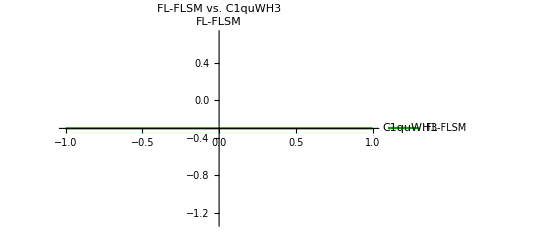

```mathematica
Plot[FLL-FLSM,{C1quWH3,-1,1},PlotStyle->{Darker[Green]},AxesLabel->{"C1quWH3","FL-FLSM"},PlotLabel->"FL-FLSM vs. C1quWH3",PlotRange->All,PlotLegends->{"FL-FLSM"}]
```

```mathematica
(* Minimum Value of CHud=12.84;CtW=-0.05;CbW=2.07;C3phiq=0*)
```

```mathematica
Clear[C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D,CHud,C3phiq,CtW,CbW]
```

```mathematica
CHud=-4.15;
CtW=-0.05;
CbW=-0.47;
C3phiq=0;
C1quWH3;
C1qdWH3=0;
C2q2H4D=0;
C3q2H4D=0;
CudH4D=0;
```

```mathematica
FLL
```

1.05914×10^-11+2.15253×10^-13 (-8.16663×10^-10+1.30299×10^-15 (-2.57339×10^12+185679. (1.7471×10^7+2.29518×10^9 C1quWH3))+4.9621×10^-11 (3.8455×10^-6-2.14928×10^-20 (0.+326214. (0.+179579. (0.+7.5848×10^11 C1quWH3))+1.76864×10^7 (0.+4.7 (0.+1.30797×10^14 C1quWH3))+2 (0.+2 (1.17264×10^16+2.08604×10^18 C1quWH3)))))+2.15253×10^-19 (2.55516×10^-18 (-2.57339×10^12+185679. (1.7471×10^7+2.29518×10^9 C1quWH3))+1.57986×10^-10 (0.+46419.8 (0.-6.98838×10^8 C1quWH3)-2.06113×10^6 (0.-1.1113×10^6 C1quWH3)-1.95977×10^7 (0.-9.4 (0.+83596.5 C1quWH3)))-4.16454×10^-7 (3.8455×10^-6-2.14928×10^-20 (0.+326214. (0.+179579. (0.+7.5848×10^11 C1quWH3))+1.76864×10^7 (0.+4.7 (0.+1.30797×10^14 C1quWH3))+2 (0.+2 (1.17264×10^16+2.08604×10^18 C1quWH3))))+4.9621×10^-11 (-2.14928×10^-20 (0.+2 (0.+2 (0.-1.42181×10^22 C1quWH3)))-4.21472×10^-23 (0.+326214. (0.+179579. (0.+7.5848×10^11 C1quWH3))+1.76864×10^7 (0.+4.7 (0.+1.30797×10^14 C1quWH3))+2 (0.+2 (1.17264×10^16+2.08604×10^18 C1quWH3)))+0.00196099 (3.8455×10^-6-2.14928×10^-20 (0.+326214. (0.+179579. (0.+7.5848×10^11 C1quWH3))+1.76864×10^7 (0.+4.7 (0.+1.30797×10^14 C1quWH3))+2 (0.+2 (1.17264×10^16+2.08604×10^18 C1quWH3))))))

```mathematica
FLL
```

9.3749×10^-13

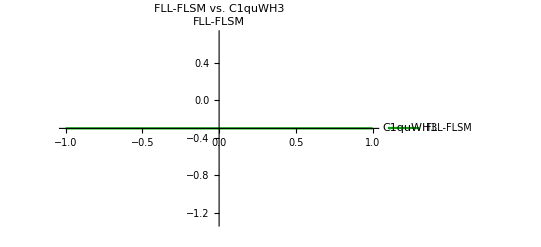

```mathematica
Plot[FLL-FLSM,{C1quWH3,-1,1},PlotStyle->{Darker[Green]},AxesLabel->{"C1quWH3 ","FLL-FLSM"},PlotLabel->"FLL-FLSM vs. C1quWH3 ",PlotRange->All,PlotLegends->{"FLL-FLSM"}]
```

```mathematica
(* Maximum Value of CHud=12.84;CtW=0.17;CbW=2.07;C3phiq=0*)
```

```mathematica
Clear[C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D,CHud,C3phiq,CtW,CbW]
```

```mathematica
CHud=12.84;
CtW=0.17;
CbW=2.07;
C3phiq=0;
C1quWH3=0;
C1qdWH3;
C2q2H4D=0;
C3q2H4D=0;
CudH4D=0;
```

```mathematica
FLL
```

9.27065×10^-13+2.15253×10^-13 (2.35486×10^-10+1.09809×10^-16 (8.51602×10^12-3.20117×10^12 Conjugate[C1qdWH3])+4.1818×10^-12 (3.54512×10^-6-1.8113×10^-21 (5.42228×10^17+5.60215×10^24 Conjugate[C1qdWH3])))+2.15253×10^-19 (2.06754×10^-19 (8.51602×10^12-3.20117×10^12 Conjugate[C1qdWH3])+1.33143×10^-11 (0.-3.94809×10^11 Conjugate[C1qdWH3])+1.25069×10^-7 (3.54512×10^-6-1.8113×10^-21 (5.42228×10^17+5.60215×10^24 Conjugate[C1qdWH3]))+4.1818×10^-12 (-1.8113×10^-21 (0.-3.93265×10^21 Conjugate[C1qdWH3])-3.41041×10^-24 (5.42228×10^17+5.60215×10^24 Conjugate[C1qdWH3])+0.00188285 (3.54512×10^-6-1.8113×10^-21 (5.42228×10^17+5.60215×10^24 Conjugate[C1qdWH3]))))

```mathematica
FLSM
```

0.301225

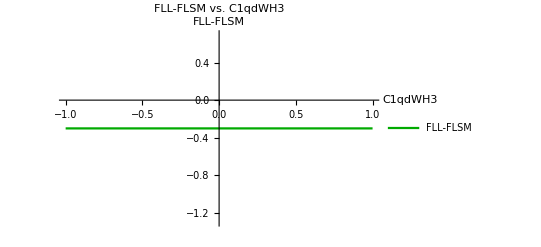

```mathematica
Plot[FLL-FLSM,{C1qdWH3,-1,1},PlotStyle->{Darker[Green]},AxesLabel->{"C1qdWH3 ","FLL-FLSM"},PlotLabel->"FLL-FLSM vs. C1qdWH3 ",PlotRange->All,PlotLegends->{"FLL-FLSM"}]
```

```mathematica
(* Minimum Value of CHud=12.84;CtW=-0.05;CbW=2.07;C3phiq=0*)
```

```mathematica
Clear[C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D,CHud,C3phiq,CtW,CbW]
```

```mathematica
CHud=-4.15;
CtW=-0.05;
CbW=-0.47;
C3phiq=0;
C1quWH3=0;
C1qdWH3;
C2q2H4D=0;
C3q2H4D=0;
CudH4D=0;
```

```mathematica
FLL
```

1.05914×10^-11+2.15253×10^-13 (-8.16663×10^-10+4.9621×10^-11 (3.8455×10^-6-2.14928×10^-20 (4.69056×10^16-1.58426×10^24 Conjugate[C1qdWH3]))+1.30299×10^-15 (6.70605×10^11-3.20117×10^12 Conjugate[C1qdWH3]))+2.15253×10^-19 (-4.16454×10^-7 (3.8455×10^-6-2.14928×10^-20 (4.69056×10^16-1.58426×10^24 Conjugate[C1qdWH3]))+2.55516×10^-18 (6.70605×10^11-3.20117×10^12 Conjugate[C1qdWH3])+1.57986×10^-10 (0.+1.1079×10^11 Conjugate[C1qdWH3])+4.9621×10^-11 (0.00196099 (3.8455×10^-6-2.14928×10^-20 (4.69056×10^16-1.58426×10^24 Conjugate[C1qdWH3]))-4.21472×10^-23 (4.69056×10^16-1.58426×10^24 Conjugate[C1qdWH3])-2.14928×10^-20 (0.+1.15666×10^21 Conjugate[C1qdWH3])))

```mathematica
Plot[FLL-FLSM,{C1qdWH3,-1,1},PlotStyle->{Darker[Green]},AxesLabel->{"C1qdWH3 ","FLL-FLSM"},PlotLabel->"FLL-FLSM vs. C1qdWH3 ",PlotRange->All,PlotLegends->{"FLL-FLSM"}]
```

-Graphics-

```mathematica
(* Maximum Value of CHud=12.84;CtW=0.17;CbW=2.07;C3phiq=0*)
```

```mathematica
Clear[C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D,CHud,C3phiq,CtW,CbW]
```

```mathematica
CHud=12.84;
CtW=0.17;
CbW=2.07;
C3phiq=0;
C1quWH3=0;
C1qdWH3=0;
C2q2H4D;
C3q2H4D=0;
CudH4D=0;
```

```mathematica
FLL
```

9.27065×10^-13+2.15253×10^-13 (2.35486×10^-10+1.09809×10^-16 (-2.89845×10^13+185679. (2.01964×10^8+7.53802×10^8 C2q2H4D+27455.5 (0.+27455.5 Conjugate[C2q2H4D])))+4.1818×10^-12 (3.54512×10^-6-1.8113×10^-21 (0.-1.0093×10^6 (0.+179579. (0.+4.09828×10^11 C2q2H4D+4.09828×10^11 Conjugate[C2q2H4D]))+2 (0.+2 (1.35557×10^17+1.51589×10^18 (C2q2H4D+Conjugate[C2q2H4D])))-7.78954×10^7 (0.+4.7 (0.-32941.8 (0.-3.67533×10^9 (C2q2H4D+Conjugate[C2q2H4D])))))))+2.15253×10^-19 (2.06754×10^-19 (-2.89845×10^13+185679. (2.01964×10^8+7.53802×10^8 C2q2H4D+27455.5 (0.+27455.5 Conjugate[C2q2H4D])))+1.33143×10^-11 (0.+46419.8 (0.+7.80362×10^8 C2q2H4D+4.59036×10^9 (0.+0.17 Conjugate[C2q2H4D]))+9.07775×10^6 (0.+225.743 (0.-1616.8 (C2q2H4D+Conjugate[C2q2H4D])))+6.06348×10^7 (0.-9.4 (0.+27455.5 (C2q2H4D+Conjugate[C2q2H4D]))))+1.25069×10^-7 (3.54512×10^-6-1.8113×10^-21 (0.-1.0093×10^6 (0.+179579. (0.+4.09828×10^11 C2q2H4D+4.09828×10^11 Conjugate[C2q2H4D]))+2 (0.+2 (1.35557×10^17+1.51589×10^18 (C2q2H4D+Conjugate[C2q2H4D])))-7.78954×10^7 (0.+4.7 (0.-32941.8 (0.-3.67533×10^9 (C2q2H4D+Conjugate[C2q2H4D]))))))+4.1818×10^-12 (-1.8113×10^-21 (0.+2 (0.+2 (0.+2.14991×10^22 (C2q2H4D+Conjugate[C2q2H4D]))))-3.41041×10^-24 (0.-1.0093×10^6 (0.+179579. (0.+4.09828×10^11 C2q2H4D+4.09828×10^11 Conjugate[C2q2H4D]))+2 (0.+2 (1.35557×10^17+1.51589×10^18 (C2q2H4D+Conjugate[C2q2H4D])))-7.78954×10^7 (0.+4.7 (0.-32941.8 (0.-3.67533×10^9 (C2q2H4D+Conjugate[C2q2H4D])))))+0.00188285 (3.54512×10^-6-1.8113×10^-21 (0.-1.0093×10^6 (0.+179579. (0.+4.09828×10^11 C2q2H4D+4.09828×10^11 Conjugate[C2q2H4D]))+2 (0.+2 (1.35557×10^17+1.51589×10^18 (C2q2H4D+Conjugate[C2q2H4D])))-7.78954×10^7 (0.+4.7 (0.-32941.8 (0.-3.67533×10^9 (C2q2H4D+Conjugate[C2q2H4D]))))))))

```mathematica
FLSM
```

0.301225

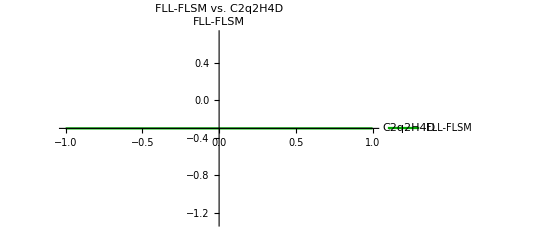

```mathematica
Plot[FLL-FLSM,{C2q2H4D,-1,1},PlotStyle->{Darker[Green]},AxesLabel->{"C2q2H4D ","FLL-FLSM"},PlotLabel->"FLL-FLSM vs. C2q2H4D ",PlotRange->All,PlotLegends->{"FLL-FLSM"}]
```

```mathematica
(* Minimum Value of CHud=12.84;CtW=-0.05;CbW=2.07;C3phiq=0*)
```

```mathematica
Clear[C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D,CHud,C3phiq,CtW,CbW]
```

```mathematica
CHud=-4.15;
CtW=-0.05;
CbW=-0.47;
C3phiq=0;
C1quWH3=0;
C1qdWH3=0;
C2q2H4D;
C3q2H4D=0;
CudH4D=0;
```

```mathematica
FLL
```

1.05914×10^-11+2.15253×10^-13 (-8.16663×10^-10+1.30299×10^-15 (-2.57339×10^12+185679. (1.7471×10^7+7.53802×10^8 C2q2H4D+27455.5 (0.+27455.5 Conjugate[C2q2H4D])))+4.9621×10^-11 (3.8455×10^-6-2.14928×10^-20 (0.+326214. (0.+179579. (0.+4.09828×10^11 C2q2H4D+4.09828×10^11 Conjugate[C2q2H4D]))+2 (0.+2 (1.17264×10^16+1.51589×10^18 (C2q2H4D+Conjugate[C2q2H4D])))+1.76864×10^7 (0.+4.7 (0.-32941.8 (0.-3.67533×10^9 (C2q2H4D+Conjugate[C2q2H4D])))))))+2.15253×10^-19 (2.55516×10^-18 (-2.57339×10^12+185679. (1.7471×10^7+7.53802×10^8 C2q2H4D+27455.5 (0.+27455.5 Conjugate[C2q2H4D])))+1.57986×10^-10 (0.+46419.8 (0.-2.29518×10^8 C2q2H4D+4.59036×10^9 (0.-0.05 Conjugate[C2q2H4D]))-2.06113×10^6 (0.+225.743 (0.-1616.8 (C2q2H4D+Conjugate[C2q2H4D])))-1.95977×10^7 (0.-9.4 (0.+27455.5 (C2q2H4D+Conjugate[C2q2H4D]))))-4.16454×10^-7 (3.8455×10^-6-2.14928×10^-20 (0.+326214. (0.+179579. (0.+4.09828×10^11 C2q2H4D+4.09828×10^11 Conjugate[C2q2H4D]))+2 (0.+2 (1.17264×10^16+1.51589×10^18 (C2q2H4D+Conjugate[C2q2H4D])))+1.76864×10^7 (0.+4.7 (0.-32941.8 (0.-3.67533×10^9 (C2q2H4D+Conjugate[C2q2H4D]))))))+4.9621×10^-11 (-2.14928×10^-20 (0.+2 (0.+2 (0.-6.32326×10^21 (C2q2H4D+Conjugate[C2q2H4D]))))-4.21472×10^-23 (0.+326214. (0.+179579. (0.+4.09828×10^11 C2q2H4D+4.09828×10^11 Conjugate[C2q2H4D]))+2 (0.+2 (1.17264×10^16+1.51589×10^18 (C2q2H4D+Conjugate[C2q2H4D])))+1.76864×10^7 (0.+4.7 (0.-32941.8 (0.-3.67533×10^9 (C2q2H4D+Conjugate[C2q2H4D])))))+0.00196099 (3.8455×10^-6-2.14928×10^-20 (0.+326214. (0.+179579. (0.+4.09828×10^11 C2q2H4D+4.09828×10^11 Conjugate[C2q2H4D]))+2 (0.+2 (1.17264×10^16+1.51589×10^18 (C2q2H4D+Conjugate[C2q2H4D])))+1.76864×10^7 (0.+4.7 (0.-32941.8 (0.-3.67533×10^9 (C2q2H4D+Conjugate[C2q2H4D]))))))))

```mathematica
Plot[FLL-FLSM,{C2q2H4D,-1,1},PlotStyle->{Darker[Green]},AxesLabel->{"C2q2H4D ","FLL-FLSM"},PlotLabel->"FLL-FLSM vs. C2q2H4D ",PlotRange->All,PlotLegends->{"FLL-FLSM"}]
```

-Graphics-

```mathematica
(* Maximum Value of CHud=12.84;CtW=0.17;CbW=2.07;C3phiq=0*)
```

```mathematica
Clear[C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D,CHud,C3phiq,CtW,CbW]
```

```mathematica
CHud=12.84;
CtW=0.17;
CbW=2.07;
C3phiq=0;
C1quWH3=0;
C1qdWH3=0;
C2q2H4D=0;
C3q2H4D;
CudH4D=0;
```

```mathematica
FLL
```

9.27065×10^-13+2.15253×10^-13 (2.35486×10^-10+1.09809×10^-16 (-2.89845×10^13+185679. (2.01964×10^8+7.53802×10^8 C3q2H4D+27455.5 (0.-27455.5 Re[C3q2H4D])))+4.1818×10^-12 (3.54512×10^-6-1.8113×10^-21 (0.+2 (0.+2 (1.35557×10^17+1.51589×10^18 (C3q2H4D-Re[C3q2H4D])))-1.0093×10^6 (0.+179579. (0.+4.09828×10^11 C3q2H4D-4.09828×10^11 Re[C3q2H4D]))-7.78954×10^7 (0.+4.7 (0.-32941.8 (-3.67533×10^9 C3q2H4D+3.67533×10^9 Re[C3q2H4D]))))))+2.15253×10^-19 (2.06754×10^-19 (-2.89845×10^13+185679. (2.01964×10^8+7.53802×10^8 C3q2H4D+27455.5 (0.-27455.5 Re[C3q2H4D])))+1.33143×10^-11 (0.+9.07775×10^6 (0.+225.743 (0.-1616.8 (C3q2H4D-Re[C3q2H4D])))+6.06348×10^7 (0.-9.4 (0.+27455.5 (C3q2H4D-Re[C3q2H4D])))+46419.8 (0.+7.80362×10^8 C3q2H4D+4.59036×10^9 (0.-0.17 Re[C3q2H4D])))+1.25069×10^-7 (3.54512×10^-6-1.8113×10^-21 (0.+2 (0.+2 (1.35557×10^17+1.51589×10^18 (C3q2H4D-Re[C3q2H4D])))-1.0093×10^6 (0.+179579. (0.+4.09828×10^11 C3q2H4D-4.09828×10^11 Re[C3q2H4D]))-7.78954×10^7 (0.+4.7 (0.-32941.8 (-3.67533×10^9 C3q2H4D+3.67533×10^9 Re[C3q2H4D])))))+4.1818×10^-12 (-1.8113×10^-21 (0.+2 (0.+2 (0.+2.14991×10^22 (C3q2H4D-Re[C3q2H4D]))))-3.41041×10^-24 (0.+2 (0.+2 (1.35557×10^17+1.51589×10^18 (C3q2H4D-Re[C3q2H4D])))-1.0093×10^6 (0.+179579. (0.+4.09828×10^11 C3q2H4D-4.09828×10^11 Re[C3q2H4D]))-7.78954×10^7 (0.+4.7 (0.-32941.8 (-3.67533×10^9 C3q2H4D+3.67533×10^9 Re[C3q2H4D]))))+0.00188285 (3.54512×10^-6-1.8113×10^-21 (0.+2 (0.+2 (1.35557×10^17+1.51589×10^18 (C3q2H4D-Re[C3q2H4D])))-1.0093×10^6 (0.+179579. (0.+4.09828×10^11 C3q2H4D-4.09828×10^11 Re[C3q2H4D]))-7.78954×10^7 (0.+4.7 (0.-32941.8 (-3.67533×10^9 C3q2H4D+3.67533×10^9 Re[C3q2H4D])))))))

```mathematica
FLSM
```

0.301225

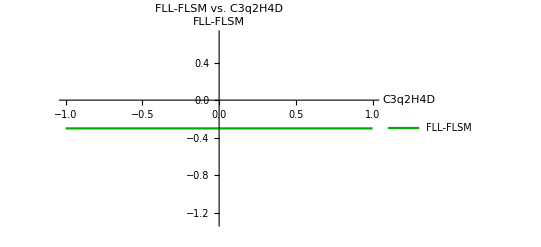

```mathematica
Plot[FLL-FLSM,{C3q2H4D,-1,1},PlotStyle->{Darker[Green]},AxesLabel->{"C3q2H4D ","FLL-FLSM"},PlotLabel->"FLL-FLSM vs. C3q2H4D ",PlotRange->All,PlotLegends->{"FLL-FLSM"}]
```

```mathematica
(* Minimum Value of CHud=12.84;CtW=-0.05;CbW=2.07;C3phiq=0*)
```

```mathematica
Clear[C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D,CHud,C3phiq,CtW,CbW]
```

```mathematica
CHud=-4.15;
CtW=-0.05;
CbW=-0.47;
C3phiq=0;
C1quWH3=0;
C1qdWH3=0;
C2q2H4D=0;
C3q2H4D;
CudH4D=0;
```

```mathematica
FLL
```

1.05914×10^-11+2.15253×10^-13 (-8.16663×10^-10+1.30299×10^-15 (-2.57339×10^12+185679. (1.7471×10^7+7.53802×10^8 C3q2H4D+27455.5 (0.-27455.5 Re[C3q2H4D])))+4.9621×10^-11 (3.8455×10^-6-2.14928×10^-20 (0.+2 (0.+2 (1.17264×10^16+1.51589×10^18 (C3q2H4D-Re[C3q2H4D])))+326214. (0.+179579. (0.+4.09828×10^11 C3q2H4D-4.09828×10^11 Re[C3q2H4D]))+1.76864×10^7 (0.+4.7 (0.-32941.8 (-3.67533×10^9 C3q2H4D+3.67533×10^9 Re[C3q2H4D]))))))+2.15253×10^-19 (2.55516×10^-18 (-2.57339×10^12+185679. (1.7471×10^7+7.53802×10^8 C3q2H4D+27455.5 (0.-27455.5 Re[C3q2H4D])))+1.57986×10^-10 (0.-2.06113×10^6 (0.+225.743 (0.-1616.8 (C3q2H4D-Re[C3q2H4D])))-1.95977×10^7 (0.-9.4 (0.+27455.5 (C3q2H4D-Re[C3q2H4D])))+46419.8 (0.-2.29518×10^8 C3q2H4D+4.59036×10^9 (0.+0.05 Re[C3q2H4D])))-4.16454×10^-7 (3.8455×10^-6-2.14928×10^-20 (0.+2 (0.+2 (1.17264×10^16+1.51589×10^18 (C3q2H4D-Re[C3q2H4D])))+326214. (0.+179579. (0.+4.09828×10^11 C3q2H4D-4.09828×10^11 Re[C3q2H4D]))+1.76864×10^7 (0.+4.7 (0.-32941.8 (-3.67533×10^9 C3q2H4D+3.67533×10^9 Re[C3q2H4D])))))+4.9621×10^-11 (-2.14928×10^-20 (0.+2 (0.+2 (0.-6.32326×10^21 (C3q2H4D-Re[C3q2H4D]))))-4.21472×10^-23 (0.+2 (0.+2 (1.17264×10^16+1.51589×10^18 (C3q2H4D-Re[C3q2H4D])))+326214. (0.+179579. (0.+4.09828×10^11 C3q2H4D-4.09828×10^11 Re[C3q2H4D]))+1.76864×10^7 (0.+4.7 (0.-32941.8 (-3.67533×10^9 C3q2H4D+3.67533×10^9 Re[C3q2H4D]))))+0.00196099 (3.8455×10^-6-2.14928×10^-20 (0.+2 (0.+2 (1.17264×10^16+1.51589×10^18 (C3q2H4D-Re[C3q2H4D])))+326214. (0.+179579. (0.+4.09828×10^11 C3q2H4D-4.09828×10^11 Re[C3q2H4D]))+1.76864×10^7 (0.+4.7 (0.-32941.8 (-3.67533×10^9 C3q2H4D+3.67533×10^9 Re[C3q2H4D])))))))

```mathematica
Plot[FLL-FLSM,{C3q2H4D,-1,1},PlotStyle->{Darker[Green]},AxesLabel->{"C3q2H4D ","FLL-FLSM"},PlotLabel->"FLL-FLSM vs. C3q2H4D ",PlotRange->All,PlotLegends->{"FLL-FLSM"}]
```

-Graphics-

```mathematica
(* Maximum Value of CHud=12.84;CtW=0.17;CbW=2.07;C3phiq=0*)
```

```mathematica
Clear[C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D,CHud,C3phiq,CtW,CbW]
```

```mathematica
CHud=12.84;
CtW=0.17;
CbW=2.07;
C3phiq=0;
C1quWH3=0;
C1qdWH3=0;
C2q2H4D=0;
C3q2H4D=0;
CudH4D;
```

```mathematica
FLL
```

9.27065×10^-13+2.15253×10^-13 (2.35486×10^-10+4.1818×10^-12 (3.54512×10^-6-1.8113×10^-21 (0.-1.0093×10^6 (0.-2.33825×10^18 Conjugate[CudH4D])+2 (2.71114×10^17-9.5425×10^16 Conjugate[CudH4D])-7.78954×10^7 (0.-1.34428×10^16 Conjugate[CudH4D])))+1.09809×10^-16 (8.51602×10^12-4.87499×10^12 Conjugate[CudH4D]))+2.15253×10^-19 (1.25069×10^-7 (3.54512×10^-6-1.8113×10^-21 (0.-1.0093×10^6 (0.-2.33825×10^18 Conjugate[CudH4D])+2 (2.71114×10^17-9.5425×10^16 Conjugate[CudH4D])-7.78954×10^7 (0.-1.34428×10^16 Conjugate[CudH4D])))+4.1818×10^-12 (0.00188285 (3.54512×10^-6-1.8113×10^-21 (0.-1.0093×10^6 (0.-2.33825×10^18 Conjugate[CudH4D])+2 (2.71114×10^17-9.5425×10^16 Conjugate[CudH4D])-7.78954×10^7 (0.-1.34428×10^16 Conjugate[CudH4D])))-1.8113×10^-21 (0.+2 (0.-1.82013×10^21 Conjugate[CudH4D]))-3.41041×10^-24 (0.-1.0093×10^6 (0.-2.33825×10^18 Conjugate[CudH4D])+2 (2.71114×10^17-9.5425×10^16 Conjugate[CudH4D])-7.78954×10^7 (0.-1.34428×10^16 Conjugate[CudH4D])))+2.06754×10^-19 (8.51602×10^12-4.87499×10^12 Conjugate[CudH4D])+1.33143×10^-11 (0.-1.26169×10^12 Conjugate[CudH4D]+6.06348×10^7 (0.+8988.96 Conjugate[CudH4D])+9.07775×10^6 (0.+225.743 (0.+56.3131 Conjugate[CudH4D]))))

```mathematica
FLSM
```

0.301225

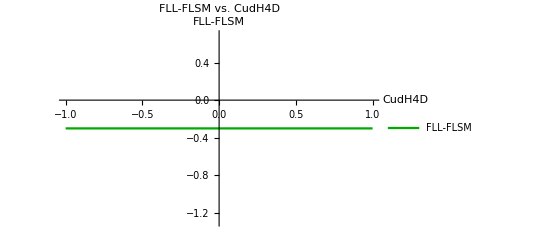

```mathematica
Plot[FLL-FLSM,{CudH4D,-1,1},PlotStyle->{Darker[Green]},AxesLabel->{"CudH4D ","FLL-FLSM"},PlotLabel->"FLL-FLSM vs. CudH4D ",PlotRange->All,PlotLegends->{"FLL-FLSM"}]
```

```mathematica
(* Minimum Value of CHud=12.84;CtW=-0.05;CbW=2.07;C3phiq=0*)
```

```mathematica
Clear[C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D,CHud,C3phiq,CtW,CbW]
```

```mathematica
CHud=-4.15;
CtW=-0.05;
CbW=-0.47;
C3phiq=0;
C1quWH3=0;
C1qdWH3=0;
C2q2H4D=0;
C3q2H4D=0;
CudH4D;
```

```mathematica
FLL
```

1.05914×10^-11+2.15253×10^-13 (-8.16663×10^-10+4.9621×10^-11 (3.8455×10^-6-2.14928×10^-20 (0.+326214. (0.-2.33825×10^18 Conjugate[CudH4D])+2 (2.34528×10^16-9.5425×10^16 Conjugate[CudH4D])+1.76864×10^7 (0.-1.34428×10^16 Conjugate[CudH4D])))+1.30299×10^-15 (6.70605×10^11-4.87499×10^12 Conjugate[CudH4D]))+2.15253×10^-19 (-4.16454×10^-7 (3.8455×10^-6-2.14928×10^-20 (0.+326214. (0.-2.33825×10^18 Conjugate[CudH4D])+2 (2.34528×10^16-9.5425×10^16 Conjugate[CudH4D])+1.76864×10^7 (0.-1.34428×10^16 Conjugate[CudH4D])))+2.55516×10^-18 (6.70605×10^11-4.87499×10^12 Conjugate[CudH4D])+1.57986×10^-10 (0.+3.71085×10^11 Conjugate[CudH4D]-1.95977×10^7 (0.+8988.96 Conjugate[CudH4D])-2.06113×10^6 (0.+225.743 (0.+56.3131 Conjugate[CudH4D])))+4.9621×10^-11 (0.00196099 (3.8455×10^-6-2.14928×10^-20 (0.+326214. (0.-2.33825×10^18 Conjugate[CudH4D])+2 (2.34528×10^16-9.5425×10^16 Conjugate[CudH4D])+1.76864×10^7 (0.-1.34428×10^16 Conjugate[CudH4D])))-4.21472×10^-23 (0.+326214. (0.-2.33825×10^18 Conjugate[CudH4D])+2 (2.34528×10^16-9.5425×10^16 Conjugate[CudH4D])+1.76864×10^7 (0.-1.34428×10^16 Conjugate[CudH4D]))-2.14928×10^-20 (0.+2 (0.+5.35332×10^20 Conjugate[CudH4D]))))

```mathematica
Plot[FLL-FLSM,{CudH4D,-1,1},PlotStyle->{Darker[Green]},AxesLabel->{"CudH4D ","FLL-FLSM"},PlotLabel->"FLL-FLSM vs. CudH4D ",PlotRange->All,PlotLegends->{"FLL-FLSM"}]
```

-Graphics-